# Electrical Networks

To run this program, you need the aCute software in the working directory. See https://www.cise.ufl.edu/~ungor/aCute/ for details.

```mathematica
<<NDSolve`FEM` (* You also need to import the FEM (Finite Elements Method) package *)
<<CompiledFunctionTools` (* REMOVE THIS WHEN PROGRAM IS COMPLETED *)
```

```mathematica
(* Set directory to where the aCute program is. *)
 SetDirectory["/Users/eric/Google Drive/Research/Electrical Networks"]; 
(* SetDirectory["/Users/saarhersonsky/Desktop/Acute/"]; *) 
(*SetDirectory["/Users/eric/Desktop"];*)
```

## Function Definitions

```mathematica
ReadPolyFile[fileName_]:=Module[{txtFile,rawNode,lines,parsedNodeHeader,parsedNodeLines,parsedEdgeHeader,numEdges,parsedEdgeLines,parsedHoleHeader,numHoles,parsedHoleLines,edges,pointsInHoles,coordinates,bdryMarkers,numVertices},
txtFile=fileName <> ".txt";
If[!FileExistsQ[txtFile],
If[FileExistsQ[fileName],CopyFile[fileName,txtFile];,Print["File not found"]]
];
rawNode = Import[txtFile];
lines=StringSplit[rawNode,"\n"];
parsedNodeHeader=ToExpression@StringSplit[lines[[1]]];
numVertices=parsedNodeHeader[[1]];
parsedNodeLines=ToExpression@(StringSplit@lines[[2;;numVertices+1]]);
parsedEdgeHeader=ToExpression@StringSplit[lines[[numVertices+2]]];
numEdges=parsedEdgeHeader[[1]];
parsedEdgeLines=ToExpression@(StringSplit@lines[[numVertices+3;;numVertices+numEdges+2]]);
parsedHoleHeader=ToExpression@StringSplit[lines[[numVertices+numEdges+3]]];
numHoles=parsedHoleHeader[[1]];
parsedHoleLines=ToExpression@(StringSplit@lines[[numVertices+numEdges+4;;numVertices+numEdges+numHoles+3]]);
coordinates=parsedNodeLines[[;;,{2,3}]];
bdryMarkers=parsedNodeLines[[;;,4]];
edges=parsedEdgeLines[[;;,{2,3}]];
pointsInHoles=parsedHoleLines[[;;,{2,3}]];
Assert[numVertices==Length[coordinates]];
DeleteFile[txtFile];
Return[{coordinates, bdryMarkers,edges,pointsInHoles}]
]
```

```mathematica
ReadNodeFile[fileName_]:=Module[{txtFile,rawNode,lines,parsedHeader,parsedLines,coordinates,bdryMarkers,numVertices},
txtFile=fileName <> ".txt";
If[!FileExistsQ[txtFile],
If[FileExistsQ[fileName],CopyFile[fileName,txtFile];,Print["File not found"]]
];
rawNode = Import[txtFile];
lines=StringSplit[rawNode,"\n"];
parsedHeader=ToExpression@StringSplit[lines[[1]]];
parsedLines=ToExpression@(StringSplit@lines[[2;;]]);
coordinates=parsedLines[[;;,{2,3}]];
bdryMarkers=parsedLines[[;;,4]];
numVertices=parsedHeader[[1]];
Assert[numVertices==Length[coordinates]];
DeleteFile[txtFile];
Return[{coordinates, bdryMarkers}]
]
```

```mathematica
ReadEleFile[fileName_]:=Module[{txtFile,rawEle,lines,parsedHeader,parsedLines,triangles,numTriangles},
txtFile=fileName <> ".txt";
If[!FileExistsQ[txtFile],
If[FileExistsQ[fileName],CopyFile[fileName,txtFile];,Print["File not found"]]
];
rawEle = Import[txtFile];
lines=StringSplit[rawEle,"\n"];
parsedHeader=ToExpression@StringSplit[lines[[1]]];
parsedLines=ToExpression@(StringSplit@lines[[2;;]]);
triangles=parsedLines[[;;,{2,3,4}]];
numTriangles=parsedHeader[[1]];
Assert[numTriangles==Length[triangles]];
DeleteFile[txtFile];
Return[triangles]
]
```

```mathematica
readData[fullFileStem_]:=Module[{regionCoordinates,regionBdryMarkers,regionEdges,pointsToDeviateForOmega0,pointsInHoles,coordinates,bdryMarkers,triangles,topology,omega0Seq},
{regionCoordinates,regionBdryMarkers,regionEdges,pointsInHoles}=ReadPolyFile[fullFileStem<>".poly"];
{coordinates,bdryMarkers}=ReadNodeFile[fullFileStem<>".node"];
triangles=ReadEleFile[fullFileStem<>".ele"];
topology=ReadEleFile[fullFileStem<>".topo.ele"];
AppendTo[pointsInHoles,pointsInHoles[[-1]]]; (* Modify pointsInHoles to include an extra copy of the last hole *)
Return[{regionCoordinates,regionBdryMarkers,regionEdges,pointsInHoles,coordinates,bdryMarkers,triangles,topology}]
]
```

```mathematica
makeRegionData[regionCoordinates_,regionEdges_,pointsInHoles_,epsilon_]:=Module[{componentEndingVertices,regionBdryComponents,exteriorVertices,interiorVerticesByHole,region,regionSkeleton,nHoles,nClasses,selectedInteriorBdryPoints,selectedExteriorBdryPoint,omega0SeqInterior,omega0SeqExterior,omega0Seq},
componentEndingVertices=Flatten@Position[Differences@regionEdges[[;;,2]],x_/;x<0]+1;
PrependTo[componentEndingVertices,0];
regionBdryComponents=Table[Range[componentEndingVertices[[i]]+1,componentEndingVertices[[i+1]]],{i,Length[componentEndingVertices]-1}];
exteriorVertices=regionBdryComponents[[1]];
interiorVerticesByHole=regionBdryComponents[[2;;]];
region=If[nHoles==1,
BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ]],
BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]]
];
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};
nHoles=Length[interiorVerticesByHole];
nClasses=nHoles+1;
selectedInteriorBdryPoints=interiorVerticesByHole[[;;,1]];
selectedExteriorBdryPoint=exteriorVertices[[1]];
omega0SeqInterior=regionCoordinates[[selectedInteriorBdryPoints]]+Map[(epsilon*#/Norm[#])&,regionCoordinates[[selectedInteriorBdryPoints]]-pointsInHoles[[;;-2]]];
omega0SeqExterior=regionCoordinates[[selectedExteriorBdryPoint]]+Map[(epsilon*#/Norm[#])&,-regionCoordinates[[selectedExteriorBdryPoint]]+pointsInHoles[[-1]]];
omega0Seq=Join[omega0SeqInterior,{omega0SeqExterior}];
Return[{exteriorVertices,interiorVerticesByHole,region,regionSkeleton,nHoles,nClasses,omega0Seq}]
]
```

```mathematica
ShowRegionSkeleton[regionSkeleton_]:=Show[Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}] ]
```

```mathematica
ShowHoleNumbers[pointsInHoles_]:=Show[Table[Graphics[Text[ToString[i],pointsInHoles[[i]] ]],{i,Length[pointsInHoles]}]]
```

```mathematica
FluxContributingEdgesCompiled::usage="Find all edges that contribute terms to the expression for computing flux. vertices is a path to compute flux across, fValues is the value of f on all vertices in a triangulation T, singularHeight is the particular value of f to treat as the singular level curve's height.";
FluxContributingEdgesCompiled=Compile[{{vertices,_Integer,1},{fValues,_Real,1},{singularHeight,_Real},{vertexTopology,_Integer,2}},Module[{n,m,nContributingEdges,contributingEdges,i,j,v},
n=Length[vertices];
m=Length[vertexTopology[[1]] ];
nContributingEdges=0;
contributingEdges=Table[0,{m*n},{2}];
For[i=1,i≤n,i++,
For[j=1,j≤m,j++,
v=vertexTopology[[vertices[[i]] ]][[j]];
If[v==0,Break[] ];
If[fValues[[v]]<singularHeight&&!MemberQ[vertices, v],
nContributingEdges=nContributingEdges+1;
contributingEdges[[nContributingEdges]]={vertices[[i]],v};
];
];
];
Return[contributingEdges[[1;;nContributingEdges]]]
]
];
```

```mathematica
FluxOnTriangulation[edges_,conductanceAssociation_,g_,TCoordinates_]:=Module[{n,result},
n = Length[edges];
result=Sum[conductanceAssociation[edges[[i]] ]*Abs[
g@@TCoordinates[[edges[[i,1]] ]] -
g@@TCoordinates[[edges[[i,2]]  ]] 
],{i,n}] (* Add gsb(omega0) if gsb(omega0)≠0 *)
]
```

```mathematica
StarPoints[{x_,y_},r_,R_,nCirclePoints_]:=Riffle[Map[RotationMatrix[-(Pi/nCirclePoints)].#&,CirclePoints[R, nCirclePoints] ], CirclePoints[r, nCirclePoints]] + Table[{x,y},{nCirclePoints*2} ]
```

```mathematica
(* GSB::usage="New and improved \\overline{g^*} function computation";
GSB[omega0_,omega_,conductanceAssociation_,toRightOfEdgePolyAssociation_,g_,TCoordinates_,LambdaGraph_]:=Module[{gammaLambda,edges,n,gsb},
gammaLambda = FindShortestPath[LambdaGraph, omega0, omega];
edges = EdgesCompiled[gammaLambda];
n = Length[edges];
gsb=Sum[conductanceAssociation[{toRightOfEdgePolyAssociation[edges[[i]] ],toRightOfEdgePolyAssociation[Reverse[edges[[i]] ] ]}]*(
g@@TCoordinates[[toRightOfEdgePolyAssociation[edges[[i]] ] ]] -
g@@TCoordinates[[toRightOfEdgePolyAssociation[Reverse[edges[[i]] ] ] ]] 
),{i,n}] (* Add gsb(omega0) if gsb(omega0)≠0 *)
] *)
```

```mathematica
VertexTopologyBuilderCompiled::usage="Build a datastructure where the ith row is all vertices connected by an edge to vertex i";
VertexTopologyBuilderCompiled=Compile[{{nVertices,_Integer},{edges,_Integer,2}},Module[{nEdges,nNeighborsList,maxValenceInitial,maxValenceActual,topology,i,v1,v2},
nEdges=Length[edges];
nNeighborsList=Table[0,{nVertices}];
maxValenceInitial=50;
topology=Table[0,{nVertices},{maxValenceInitial}];
For[i=1,i≤nEdges,i++,
v1=edges[[i,1]];
v2=edges[[i,2]];
nNeighborsList[[v1]]=nNeighborsList[[v1]]+1;
nNeighborsList[[v2]]=nNeighborsList[[v2]]+1;
topology[[v1,nNeighborsList[[v1]] ]]=v2;
topology[[v2,nNeighborsList[[v2]] ]]=v1;
];
maxValenceActual=Max[nNeighborsList];
Return[topology[[1;;nVertices,1;;maxValenceActual]] ]
]
];
```

```mathematica
NeighborsCompiled::usage="Take a vertex and a triangulation and return all vertices in the triangulation that are neighbors of the given vertex";
NeighborsCompiled=Compile[{{vertex,_Integer},{edges,_Integer,2}},Module[{n,neighbors,nNeighbors,i,result},
n=Length[edges];
neighbors=Table[0,{n}];
nNeighbors=0;
For[i=1,i≤n,i++,
If[edges[[i,1]]==vertex,
nNeighbors=nNeighbors+1;
neighbors[[nNeighbors]]=edges[[i,2]];
];
If[edges[[i,2]]==vertex,
nNeighbors=nNeighbors+1;
neighbors[[nNeighbors]]=edges[[i,1]];
];
];
result=neighbors[[1;;nNeighbors]];
Return[result]
]
];
```

```mathematica
NeighborsOrderedCompiled::usage="Take an interior vertex and a vertexTopology and return all vertices in the triangulation that are neighbors of the given vertex in either counterclockwise or clockwise order. Will fail SILENTLY on boundary vertices.";
NeighborsOrderedCompiled=Compile[{{vertex,_Integer},{vertexTopology,_Integer,2}},Module[{maxValence,n,neighbors,nNeighbors,i,j,result,neighborsExtended},
maxValence=Length[vertexTopology[[1]] ];
neighborsExtended = vertexTopology[[vertex]];
nNeighbors=maxValence;
For[j=1,j≤maxValence,j++,
If[neighborsExtended[[j]]==0,
nNeighbors=j-1;
Break[];
,];
];
neighbors = neighborsExtended[[1;;nNeighbors]];
result=Table[0,{nNeighbors}];
result[[1]]=neighbors[[1]];
(* There will always be two intersections between two rings of neighbors. In the first iteration, pick one arbitrarily, since we don't care if counterclockwise or clockwise. *)
For[j=1,j≤maxValence,j++,
If[MemberQ[neighbors,vertexTopology[[result[[1]],j]] ],
result[[2]]=vertexTopology[[result[[1]],j]];
Break[];
,];
];
(* Now continue chaining together elements of neighbors connected to the previously added element of result *)
For[i=2,i≤nNeighbors-1,i++,
For[j=1,j≤maxValence,j++,
If[MemberQ[neighbors,vertexTopology[[result[[i]],j]] ] && vertexTopology[[result[[i]],j]]≠ result[[i-1]],
result[[i+1]]=vertexTopology[[result[[i]],j]];
Break[];
,
];
];
];
Return[result]
]
];
```

```mathematica
TriangulationConnectedQCompiled=Compile[{{triangleList,_Integer,2}},Module[{nTriangles,connectedClass,nAllVertices,updatedFlag,i,alreadyUsed},
nTriangles=Length[triangleList];
nAllVertices=Length[Union[Flatten[triangleList]]];
connectedClass=triangleList[[1]];
alreadyUsed=Table[0,{nTriangles}];
alreadyUsed[[1]]=1;
updatedFlag=True;
While[updatedFlag,
updatedFlag=False;
If[Length[connectedClass]==nAllVertices,Return[True],];
For[i=1,i≤nTriangles,i++,
If[alreadyUsed[[i]]==1,Continue[],];
If[IntersectingQ[connectedClass,triangleList[[i]] ],
connectedClass=Union[Join[connectedClass, triangleList[[i]] ] ];
alreadyUsed[[i]]=1;
updatedFlag=True;
,
];
];
];
Return[False]
]
];
```

```mathematica
(* NOT COMPLETELY COMPILED *)TriangulationConnectedComponentsCompiled=Compile[{{triangleList,_Integer,2}},Module[{nTriangles,nAllVertices,updatedFlag,i,alreadyUsed,connectedClassList,connectedClassLengths,nConnectedClasses,terminate},
nTriangles=Length[triangleList];
(* nAllVertices=Length[Union[Flatten[triangleList]]]; *)
connectedClassList=Table[0,{100},{nTriangles}];
connectedClassLengths=Table[0,{100}];
nConnectedClasses=0;
alreadyUsed=Table[0,{nTriangles}];
terminate=False;
While[True,
(* Find a starting point for a new connected component *)
terminate=True;
For[i=1,i≤nTriangles,i++,
If[alreadyUsed[[i]]==0,
alreadyUsed[[i]]=1;
nConnectedClasses=nConnectedClasses+1;
connectedClassList[[nConnectedClasses,1]]=i;
connectedClassLengths[[nConnectedClasses]]=connectedClassLengths[[nConnectedClasses]]+1;
terminate=False;
Break[];
,
];
];
If[terminate,Break[];];
updatedFlag=True;
While[updatedFlag,
updatedFlag=False;
For[i=1,i≤nTriangles,i++,
If[alreadyUsed[[i]]==1,Continue[],];
If[IntersectingQ[Flatten[triangleList[[connectedClassList[[nConnectedClasses,1;;connectedClassLengths[[nConnectedClasses]] ]] ]] ],triangleList[[i]] ],
alreadyUsed[[i]]=1;
connectedClassLengths[[nConnectedClasses]]=connectedClassLengths[[nConnectedClasses]]+1;
connectedClassList[[nConnectedClasses,connectedClassLengths[[nConnectedClasses]] ]]=i;
updatedFlag=True;
,
];
];
];
];
Return[connectedClassList[[1;;nConnectedClasses]] ]
]
];
```

```mathematica
TriangulationConnectedComponents[triangleList_]:=Module[{struct,connectedComponents},
struct=TriangulationConnectedComponentsCompiled[triangleList];
connectedComponents=DeleteCases[struct,0,{2}]
]
```

```mathematica
IndexFunction[vertex_,vertexTopology_,coordinates_]:=SignChanges[f@@@coordinates[[NeighborsOrderedCompiled[vertex,vertexTopology ] ]],f@@coordinates[[vertex]] ]
```

```mathematica
SignChanges::usage = "SignChanges[{{list,_Real,1},{value,_Real}}] returns the number of sign changes in the looped vector {list[[1]]-value, list[[2]]-value, ..., list[[n]]-value, list[[1]]-value}.";
SignChanges=Compile[{{list,_Real,1},{value,_Real}},Module[{result,n,i},
result=0;
n=Length[list];
For[i=1,i≤n-1,i++,
If[Sign[list[[i]]-value]≠ Sign[list[[i+1]]-value],result=result+1,];
];
If[Sign[list[[n]]-value]≠ Sign[list[[1]]-value],result=result+1,];
Return[result]
]
];
```

```mathematica
PointToRightOfLineCompiled::usage = "PointToRightOfLineCompiled[{tailX, _Real},{tailY, _Real},{headX, _Real},{headY, _Real},{pointX, _Real},{pointY, _Real}] returns True if the point (pointX, pointY) is to the right of the oriented line from (tail) to (head).";
PointToRightOfLineCompiled = Compile[{{tailX, _Real}, {tailY, _Real}, {headX, _Real},{headY, _Real}, {pointX, _Real}, {pointY, _Real}},(headY - tailY)*(pointX - tailX) - (headX - tailX)*(pointY - tailY)> 0
];
```

```mathematica
PolygonalAnnulus[n_, innerRadius_, outerRadius_:1] := Module[{points, extV, intV, vertices},
points = Table[{N[Cos[2*Pi*(i - 1)/n + Pi/2]], N[Sin[2*Pi*(i - 1)/n + Pi/2]]},{i, n}];
extV =outerRadius*points;
intV = innerRadius*points;
vertices = Join[extV, intV];
Return[{vertices, Range[n],n +Range[n]}]
]
```

```mathematica
PolygonPathToVertexPathCompiled=Compile[{{facesPath,_Integer,1},{paddedPolygonization,_Integer,2},{innerRingVertices,_Integer,1},{outerRingVertices,_Integer,1}},Module[{nPathPolygons,nPolygons,maxPolygonLength,nextPolygon,currentVertex,nextVertex,vertexPath,nVertexPath,currentPolygonIndex,currentPolygon,i},
nPathPolygons=Length[facesPath];
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
currentPolygon=Table[0,{maxPolygonLength}];
nextPolygon=Table[0,{maxPolygonLength}];
currentVertex=1;
nextVertex=2;
nVertexPath=2;
vertexPath=Table[0,{maxPolygonLength*nPathPolygons}];
(* For first polygon in facesPath *)
currentPolygonIndex=1;
currentPolygon=paddedPolygonization[[facesPath[[currentPolygonIndex]] ]];
While[!(MemberQ[innerRingVertices,currentPolygon[[currentVertex]] ]&&!MemberQ[innerRingVertices,currentPolygon[[nextVertex]] ]),
currentVertex=nextVertex;
If[currentVertex==maxPolygonLength||currentPolygon[[currentVertex+1]]==0,
nextVertex=1,
nextVertex=currentVertex+1
];
];
vertexPath[[1]]=currentPolygon[[currentVertex]];
vertexPath[[2]]=currentPolygon[[nextVertex]];
currentVertex=nextVertex;
(* For intermediate polygons in facesPath *)
For[currentPolygonIndex=1,currentPolygonIndex<nPathPolygons,currentPolygonIndex++,
currentPolygon=paddedPolygonization[[facesPath[[currentPolygonIndex]] ]];
nextPolygon=paddedPolygonization[[facesPath[[currentPolygonIndex+1]] ]];
(* Traverse new polygon until position lines up with vertexPath *)
While[vertexPath[[nVertexPath]]≠currentPolygon[[currentVertex]],
currentVertex=nextVertex;
If[currentVertex==maxPolygonLength||currentPolygon[[currentVertex+1]]==0,
nextVertex=1,
nextVertex=currentVertex+1
];
];
(* Now that alignment is done, traverse polygon while adding vertices to vertexPath until nextPolygon is reached *)
While[!MemberQ[nextPolygon,currentPolygon[[currentVertex]] ],
currentVertex=nextVertex;
If[currentVertex==maxPolygonLength||currentPolygon[[currentVertex+1]]==0,
nextVertex=1,
nextVertex=currentVertex+1
];
nVertexPath=nVertexPath+1;
vertexPath[[nVertexPath]]=currentPolygon[[currentVertex]];
];

];
(* For last polygon *)
currentPolygonIndex=nPathPolygons;
currentPolygon=paddedPolygonization[[facesPath[[currentPolygonIndex]] ]];
(* Traverse new polygon until position lines up with vertexPath *)
While[vertexPath[[nVertexPath]]≠currentPolygon[[currentVertex]],
currentVertex=nextVertex;
If[currentVertex==maxPolygonLength||currentPolygon[[currentVertex+1]]==0,
nextVertex=1,
nextVertex=currentVertex+1
];
];
(* Now that alignment is done, traverse polygon while adding vertices to vertexPath until outerRingVertices is reached *)
While[!MemberQ[outerRingVertices,currentPolygon[[currentVertex]] ],
currentVertex=nextVertex;
If[currentVertex==maxPolygonLength||currentPolygon[[currentVertex+1]]==0,
nextVertex=1,
nextVertex=currentVertex+1
];
nVertexPath=nVertexPath+1;
vertexPath[[nVertexPath]]=currentPolygon[[currentVertex]];
];
Return[Join[{nVertexPath},vertexPath]]
]
];
```

```mathematica
BoundaryConnectedClassesUnseededCompiled::usage="BoundaryConnectedClassesUnseededCompiled[{{boundaryEdges,_Integer,2}}] takes the boundary edges and constructs each connected component.";
BoundaryConnectedClassesUnseededCompiled=Compile[{{boundaryEdges,_Integer,2}},Module[{i,nBoundaryEdges,classList,alreadyUsed,start,currentVertex,position,foundFlag,nClasses,allFound},
nBoundaryEdges=Length[boundaryEdges];
classList=Table[0,{1000},{nBoundaryEdges}];
alreadyUsed=Table[0,{nBoundaryEdges}];
alreadyUsed[[1]]=1;
start=boundaryEdges[[1,1]];
currentVertex=boundaryEdges[[1,2]];
classList[[1,1]]=start;
classList[[1,2]]=currentVertex;
nClasses=1;
position=3;
(* Compute class1 *)
foundFlag=False;
allFound=False;
While[!foundFlag,
For[i=1,i≤nBoundaryEdges,i++,
If[alreadyUsed[[i]]==1,
Continue[],
If[boundaryEdges[[i,1]]==currentVertex,
If[boundaryEdges[[i,2]]==start,foundFlag=True,];
classList[[1,position]]=boundaryEdges[[i,2]];
currentVertex=boundaryEdges[[i,2]];
position=position+1;
alreadyUsed[[i]]=1;
,
]
];
];
];
classList[[1,1]]=position-2;
(* Determine if all edges have been used *)
While[!allFound,
allFound=True;
For[i=1,i≤nBoundaryEdges,i++,
If[alreadyUsed[[i]]==0,
(* If not all used, then find some unused edge to start class2 *)
allFound=False;
nClasses=nClasses+1;
start=boundaryEdges[[i,1]];
currentVertex=boundaryEdges[[i,2]];
classList[[nClasses,1]]=start;
classList[[nClasses,2]]=currentVertex;
position=3;
alreadyUsed[[i]]=1;
Break[];
,
];
];
If[allFound,Break[];];
(* Compute next connected component *)
foundFlag=False;
While[!foundFlag,
For[i=1,i≤nBoundaryEdges,i++,
If[alreadyUsed[[i]]==1,
Continue[],
If[boundaryEdges[[i,1]]==currentVertex,
If[boundaryEdges[[i,2]]==start,foundFlag=True,];
classList[[nClasses,position]]=boundaryEdges[[i,2]];
currentVertex=boundaryEdges[[i,2]];
position=position+1;
alreadyUsed[[i]]=1;
,
]
];
];
];
classList[[nClasses,1]]=position-2;
];
Return[classList[[1;;nClasses]] ]
]
];
```

```mathematica
AngleCompiled::usage="AngleCompiled[{{vector1,_Real,1}, {vector2,_Real,1}}] finds the angle between the given vectors.";
AngleCompiled=Compile[{{vector1,_Real,1}, {vector2,_Real,1}},Module[{dot,norm1,norm2,angle},
dot=vector1[[1]]*vector2[[1]]+vector1[[2]]*vector2[[2]];
norm1=Norm[vector1];
norm2=Norm[vector2];
angle=ArcCos[dot/(norm1*norm2)]
]
];
```

```mathematica
AngleCompiled::usage="AngleCompiled[{{vector1,_Real,1}, {vector2,_Real,1}}] finds the angle between the given vectors.";
AngleCompiled=Compile[{{vector1,_Real,1}, {vector2,_Real,1}},Module[{dot,norm1,norm2,angle,hold},
dot=vector1[[1]]*vector2[[1]]+vector1[[2]]*vector2[[2]];
norm1=Norm[vector1];
norm2=Norm[vector2];
hold=dot/(norm1*norm2);
If[hold≥1,hold=1.];
If[hold≤-1,hold=-1.];
angle=ArcCos[hold]
]
];
```

```mathematica
WindingNumberCompiled::usage="WindingNumber[{{pointX,_Real},{pointY,_Real},{path,_Integer,1},{coordinates,_Real,2}}] finds the winding number of the path (indices in the given list of coordiantes) with respect to the point {pointX, pointY}";
WindingNumberCompiled=Compile[{{pointX,_Real},{pointY,_Real},{path,_Integer,1},{coordinates,_Real,2}},Module[{i,nVertices,windingNumber,head1,head2,angle,sign},
nVertices=Length[path];
windingNumber=0.;
angle=0.;
sign=1.;
For[i=1,i≤nVertices,i++,
head1=coordinates[[path[[i]] ]];
head2=coordinates[[path[[Mod[i,nVertices]+1]] ]];
angle=AngleCompiled[head1 - {pointX,pointY},head2 - {pointX,pointY}];
If[PointToRightOfLineCompiled[pointX,pointY,head1[[1]],head1[[2]],head2[[1]],head2[[2]] ],
sign=-1.;
,
sign=1.;
];
windingNumber=windingNumber+sign*angle;
];
windingNumber=windingNumber/2/Pi
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
WindingNumberIntegerCompiled::usage="WindingNumber[{{pointX,_Real},{pointY,_Real},{path,_Integer,1},{coordinates,_Real,2}}] finds the winding number (rounded to the nearest integer) of the path (indices in the given list of coordiantes) with respect to the point {pointX, pointY}";
WindingNumberIntegerCompiled=Compile[{{pointX,_Real},{pointY,_Real},{path,_Integer,1},{coordinates,_Real,2}},Module[{i,nVertices,windingNumber,head1,head2,angle,sign,windingNumberResult},
nVertices=Length[path];
windingNumber=0.;
angle=0.;
sign=1.;
For[i=1,i≤nVertices,i++,
head1=coordinates[[path[[i]] ]];
head2=coordinates[[path[[Mod[i,nVertices]+1]] ]];
angle=AngleCompiled[head1 - {pointX,pointY},head2 - {pointX,pointY}];
If[PointToRightOfLineCompiled[pointX,pointY,head1[[1]],head1[[2]],head2[[1]],head2[[2]] ],
sign=-1.;
,
sign=1.;
];
windingNumber=windingNumber+sign*angle;
];
windingNumberResult=Round[windingNumber/2/Pi]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
BoundaryEdges[polygonization_]:=Module[{allEdges,tally,boundaryEdges},
allEdges=Map[EdgesWrapCompiled,polygonization];
tally=Tally[Sort/@Partition[Flatten[allEdges],2]];
boundaryEdges=Cases[tally,x_/;x[[2]]==1][[;;,1]]
]
```

```mathematica
BoundaryVertices[polygonization_]:=Module[{allEdges,tally,boundaryVertices},
allEdges=Map[EdgesWrapCompiled,polygonization];
tally=Tally[Sort/@Partition[Flatten[allEdges],2]];
boundaryVertices=Union[Flatten[Cases[tally,x_/;x[[2]]==1][[;;,1]] ] ]
]
```

```mathematica
BoundaryConnectedClasses::usage="BoundaryConnectedClasses[Lambda_, iniClasses__] takes a mesh and a sequence of inital connected classes and returns a list of the vertices in each connected component of the boundary of mesh.";
BoundaryConnectedClasses[Lambda_,iniClasses__]:=Module[{n,i,boundaryEdges,keepGoingQ,hold,hold2,classes=List[iniClasses],result},
n = Length[classes];
boundaryEdges = BoundaryEdges[Lambda[[3]] ];
result = Table[Null,{n}];
For[i=1,i≤ n,i++,
hold =classes[[i]];
keepGoingQ = True;
 While[keepGoingQ,
hold2 = Union[Flatten[Select[boundaryEdges,MemberQ[hold,#[[1]]]||MemberQ[hold,#[[2]]]&]]];
If[hold ==hold2,keepGoingQ=False,hold = hold2];
];
result[[i]]=hold;
];
Return[result]
]
```

```mathematica
BuildPolygonizationTopologyCompiled::usage="BuildPolygonizationTopologyCompiled[paddedPolygonization,_Integer,2] returns a polygonizationTopology giving the adjacent polygons across each edge of the given paddedPolygonization. 0 means that edge is a boundary edge, whereas -1 means that edge does not exist.";
BuildPolygonizationTopologyCompiled=Compile[{{paddedPolygonization,_Integer,2}},Module[{i,j,k,m,edges,nPolygons,maxPolygonLength,polygonizationTopology,edgesWrapOrdered,currentEdge,foundFlag},
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
edgesWrapOrdered=Table[0,{nPolygons},{maxPolygonLength},{2}]; (* {0,0} for non-existant *)
polygonizationTopology = Table[-1, {nPolygons},{maxPolygonLength}]; (* -1 for non-existant *)
foundFlag=False;
(* Builds the edgesWrapOrdered array *)
For[i=1, i≤nPolygons, i++,
For[j=1,j≤maxPolygonLength,j++,
If[j==maxPolygonLength,
(* When j has reached end of polygon *)
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
(* When j hasn't reached end of polygon *)
If[paddedPolygonization[[i,j+1]]==0,
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,j+1]];
];
];
];
];
(* Builds polygonizationTopology *)
For[i=1, i≤nPolygons, i++,
For[k=1,k≤maxPolygonLength,k++,
If[polygonizationTopology[[i,k]]≠-1,Continue[], (* Continue if adjacent poly already computed *)
If[edgesWrapOrdered[[i,k,1]]==0,Break[], (* Break if end of polygon *)
foundFlag=False;
currentEdge = Reverse[edgesWrapOrdered[[i,k]] ];
For[j=1,j≤nPolygons,j++,
If[foundFlag,Break[] ,
For[m=1,m≤maxPolygonLength,m++,
If[foundFlag,Break[],
If[currentEdge[[1]]==edgesWrapOrdered[[j,m,1]]&&currentEdge[[2]]==edgesWrapOrdered[[j,m,2]],
polygonizationTopology[[i,k]]=j;
polygonizationTopology[[j,m]]=i;
foundFlag=True;
,];
];
];
];
];
If[!foundFlag,polygonizationTopology[[i,k]]=0,];
];
];
];
];
Return[polygonizationTopology]
]
];
```

```mathematica
BuildPolygonizationTopologyAndBoundaryEdgesCompiled::usage="BuildPolygonizationTopologyAndBoundaryEdgesCompiled[paddedPolygonization,_Integer,2] returns a polygonizationTopology giving the adjacent polygons across each edge of the given paddedPolygonization. 0 means that edge is a boundary edge, whereas -1 means that edge does not exist.";
BuildPolygonizationTopologyAndBoundaryEdgesCompiled=Compile[{{paddedPolygonization,_Integer,2}},Module[{i,j,k,m,nBoundaryEdges,boundaryEdges,firstRow,nPolygons,maxPolygonLength,polygonizationTopology,edgesWrapOrdered,currentEdge,foundFlag},
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
edgesWrapOrdered=Table[0,{nPolygons},{maxPolygonLength},{2}]; (* {0,0} for non-existant *)
polygonizationTopology = Table[-1, {nPolygons},{maxPolygonLength}]; (* -1 for non-existant *)
nBoundaryEdges=0;
boundaryEdges=Table[0,{maxPolygonLength*nPolygons},{maxPolygonLength}];
foundFlag=False;
(* Builds the edgesWrapOrdered array *)
For[i=1, i≤nPolygons, i++,
For[j=1,j≤maxPolygonLength,j++,
If[j==maxPolygonLength,
(* When j has reached end of polygon *)
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
(* When j hasn't reached end of polygon *)
If[paddedPolygonization[[i,j+1]]==0,
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,j+1]];
];
];
];
];
(* Builds polygonizationTopology *)
For[i=1, i≤nPolygons, i++,
For[k=1,k≤maxPolygonLength,k++,
If[polygonizationTopology[[i,k]]≠-1,Continue[], (* Continue if adjacent poly already computed *)
If[edgesWrapOrdered[[i,k,1]]==0,Break[], (* Break if end of polygon *)
foundFlag=False;
currentEdge = Reverse[edgesWrapOrdered[[i,k]] ];
For[j=1,j≤nPolygons,j++,
If[foundFlag,Break[] ,
For[m=1,m≤maxPolygonLength,m++,
If[foundFlag,Break[],
If[currentEdge[[1]]==edgesWrapOrdered[[j,m,1]]&&currentEdge[[2]]==edgesWrapOrdered[[j,m,2]],
polygonizationTopology[[i,k]]=j;
polygonizationTopology[[j,m]]=i;
foundFlag=True;
,];
];
];
];
];
If[!foundFlag,
polygonizationTopology[[i,k]]=0;
nBoundaryEdges=nBoundaryEdges+1;
boundaryEdges[[nBoundaryEdges,1]]=currentEdge[[2]]; (* Remember that currentEdge was reversed *)
boundaryEdges[[nBoundaryEdges,2]]=currentEdge[[1]];
,];
];
];
];
];
firstRow=Table[0,{maxPolygonLength}];
firstRow[[1]]=nBoundaryEdges;
Return[Join[{firstRow},polygonizationTopology, boundaryEdges]]
]
];
```

```mathematica
BuildPolyTopoBdryEdgesInternalEdgesCompiled::usage="BuildPolyTopoBdryEdgesInternalEdgesCompiled[paddedPolygonization,_Integer,2] returns a polygonizationTopology giving the adjacent polygons across each edge of the given paddedPolygonization. 0 means that edge is a boundary edge, whereas -1 means that edge does not exist.";
BuildPolyTopoBdryEdgesInternalEdgesCompiled=Compile[{{paddedPolygonization,_Integer,2}},Module[{i,j,k,m,nBoundaryEdges,boundaryEdges,firstRow,nPolygons,maxPolygonLength,polygonizationTopology,edgesWrapOrdered,currentEdge,foundFlag,nInternalEdges,internalEdges},
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
edgesWrapOrdered=Table[0,{nPolygons},{maxPolygonLength},{2}]; (* {0,0} for non-existant *)
polygonizationTopology = Table[-1, {nPolygons},{maxPolygonLength}]; (* -1 for non-existant *)
nBoundaryEdges=0;
boundaryEdges=Table[0,{maxPolygonLength*nPolygons},{maxPolygonLength}];
nInternalEdges=0;
internalEdges=Table[0,{maxPolygonLength*nPolygons},{maxPolygonLength}];
foundFlag=False;
(* Builds the edgesWrapOrdered array *)
For[i=1, i≤nPolygons, i++,
For[j=1,j≤maxPolygonLength,j++,
If[j==maxPolygonLength,
(* When j has reached end of polygon *)
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
(* When j hasn't reached end of polygon *)
If[paddedPolygonization[[i,j+1]]==0,
If[paddedPolygonization[[i,j]]≠0,
(* Case where edge wraps back to first vertex *)
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,1]];
,
(* Case where there are no more edges that exist *)
Break[];
];
,
edgesWrapOrdered[[i,j,1]]=paddedPolygonization[[i,j]];
edgesWrapOrdered[[i,j,2]]=paddedPolygonization[[i,j+1]];
];
];
];
];
(* Builds polygonizationTopology *)
For[i=1, i≤nPolygons, i++,
For[k=1,k≤maxPolygonLength,k++,
If[polygonizationTopology[[i,k]]≠-1,Continue[], (* Continue if adjacent poly already computed *)
If[edgesWrapOrdered[[i,k,1]]==0,Break[], (* Break if end of polygon *)
foundFlag=False;
currentEdge = Reverse[edgesWrapOrdered[[i,k]] ];
For[j=1,j≤nPolygons,j++,
If[foundFlag,Break[] ,
For[m=1,m≤maxPolygonLength,m++,
If[foundFlag,Break[],
If[currentEdge[[1]]==edgesWrapOrdered[[j,m,1]]&&currentEdge[[2]]==edgesWrapOrdered[[j,m,2]],
polygonizationTopology[[i,k]]=j;
polygonizationTopology[[j,m]]=i;
nInternalEdges=nInternalEdges+1;
If[i≤j,
internalEdges[[nInternalEdges,1]]=i;
internalEdges[[nInternalEdges,2]]=j;
,
internalEdges[[nInternalEdges,1]]=j;
internalEdges[[nInternalEdges,2]]=i
];
foundFlag=True;
,];
];
];
];
];
If[!foundFlag,
polygonizationTopology[[i,k]]=0;
nBoundaryEdges=nBoundaryEdges+1;
boundaryEdges[[nBoundaryEdges,1]]=currentEdge[[2]]; (* Remember that currentEdge was reversed *)
boundaryEdges[[nBoundaryEdges,2]]=currentEdge[[1]];
,];
];
];
];
];
firstRow=Table[0,{maxPolygonLength}];
firstRow[[1]]=nBoundaryEdges;
firstRow[[2]]=nInternalEdges;
Return[Join[{firstRow},polygonizationTopology,boundaryEdges,internalEdges]]
]
];
```

```mathematica
DistanceCompiled::usage="DistanceCompiled[{{vector,_Integer,1},{TCoordinates,_Real,2}}] finds the length of the given vector with respect to the given coordinates";
DistanceCompiled=Compile[{{vector,_Integer,1},{TCoordinates,_Real,2}},
Norm[TCoordinates[[vector[[1]] ]]-TCoordinates[[vector[[2]] ]] ]
];
```

```mathematica
CircumcenterCompiled::usage="Circumcenter[T] takes a triangle T and returns the circumcenter of T.";
CircumcenterCompiled=Compile[{{triangle,_Integer,1},{TCoordinates,_Real,2}},Module[{a,bx,by,T},
T=TCoordinates[[#]]&/@triangle;
a = Det[Table[{T[[i,1]],T[[i,2]],1},{i,3}]];
bx = -Det[Table[{T[[i,1]]^2 + T[[i,2]]^2,T[[i,2]],1},{i,3}]];
by = Det[Table[{T[[i,1]]^2 + T[[i,2]]^2,T[[i,1]],1},{i,3}]];
Return[{-bx/(2a),-by/(2a)}]
]
];
```

```mathematica
DistanceNumericCompiled=Compile[{{pointList,_Real,2}},
Norm[pointList[[2]]-pointList[[1]] ]
];
```

```mathematica
BuildConductanceAssociation::usage="BuildConductanceAssociation[triangleList_,interiorEdges_,toRightOfEdgeTriAssociation_,TCoordinates_] builds a dictionary association between edges in the triangulation and the conductance of that edge, given by the distance between circumcenters of the adjoining triangles divided by the distance between the endpoints of the edge.";
BuildConductanceAssociation[triangleList_,interiorEdges_,toRightOfEdgeTriAssociation_,TCoordinates_]:=Module[{table,edgeAssociatedToConductance},
table=Map[{#,DistanceNumericCompiled[{
CircumcenterCompiled[triangleList[[toRightOfEdgeTriAssociation[#] ]],TCoordinates],
CircumcenterCompiled[triangleList[[toRightOfEdgeTriAssociation[Reverse[#]] ]],TCoordinates]
}]/DistanceCompiled[#,TCoordinates]}&,interiorEdges];
edgeAssociatedToConductance=Association[Table[table[[i,1]]->table[[i,2]],{i,Length[table]}]]
]
```

```mathematica
EdgesCompiled::usage="Edges[{{path,_Integer,1}}] takes a list of indices and returns the list of pairs from one index to the next.";
EdgesCompiled = Compile[{{path,_Integer,1}},
Partition[path,2,1]
];
```

```mathematica
EdgesWrapCompiled::usage="Edges[{{polygon,_Integer,1}}] takes a list of indices and returns the list of pairs from one index to the next.";
EdgesWrapCompiled=Compile[{{polygon, _Integer, 1}},
Append[Partition[polygon,2,1],{polygon[[-1]],polygon[[1]]}]
];
```

```mathematica
EdgesWrapSortCompiled::usage="EdgesWrapSortCompiled[{{polygon, _Integer, 1}}] takes a list of indices representing a polygon and returns the edges (internally sorted by index) going around the polygon.";
EdgesWrapSortCompiled=Compile[{{polygon, _Integer, 1}},
Map[Sort,Append[Partition[polygon,2,1],{polygon[[-1]], polygon[[1]]}]]
];
```

```mathematica
InteriorAndBoundaryEdgesCompiled::usage="InteriorAndBoundaryEdgesCompiled[{{triangleList,_Integer,2},{triangulationTopology,_Integer,2}}] runs the internals for InteriorAndBoundaryEdges.";
InteriorAndBoundaryEdgesCompiled=Compile[{{triangleList,_Integer,2},{triangulationTopology,_Integer,2}},Module[{nTriangles,table,counter,i,j},
nTriangles=Length[triangleList];
table=Table[0,{3*nTriangles},{3}];
counter=0;
For[i=1,i≤nTriangles,i++,
For[j=1,j≤2,j++,
If[triangulationTopology[[i,j]]==0,
counter=counter+1;
table[[counter,1]]=triangleList[[i,j]];
table[[counter,2]]=triangleList[[i,j+1]];
table[[counter,3]]=0;
,
counter=counter+1;
table[[counter,1]]=triangleList[[i,j]];
table[[counter,2]]=triangleList[[i,j+1]];
table[[counter,3]]=1;
];
];
j=3;
If[triangulationTopology[[i,j]]==0,
counter=counter+1;
table[[counter,1]]=triangleList[[i,j]];
table[[counter,2]]=triangleList[[i,1]];
table[[counter,3]]=0;
,
counter=counter+1;
table[[counter,1]]=triangleList[[i,j]];
table[[counter,2]]=triangleList[[i,1]];
table[[counter,3]]=1;
];
];
Return[table]
]
];
```

```mathematica
InteriorAndBoundaryEdges::usage="InteriorAndBoundaryEdges[triangleList_, triangulationTopology_] creates a list of interior edges and a list of boundary edges.";
InteriorAndBoundaryEdges[triangleList_, triangulationTopology_]:=Module[{interiorAndBoundaryEdges,interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation},
interiorAndBoundaryEdges=InteriorAndBoundaryEdgesCompiled[triangleList,triangulationTopology];
interiorEdgesOrientedTriangulation=Pick[interiorAndBoundaryEdges[[;;,1;;2]],interiorAndBoundaryEdges[[;;,3]]/.{0->False,1->True}];
boundaryEdgesOrientedTriangulation=Pick[interiorAndBoundaryEdges[[;;,1;;2]],interiorAndBoundaryEdges[[;;,3]]/.{1->False,0->True}];
Return[{interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation}]
];
```

```mathematica
MakePolyFile::usage="MakePolyFile[fileName_,R_, hole_] takes the given region and writes a .poly file that can be used by triangle.c and acute.c. It assumes dimensions is 2, numAttr is 0, and numBoundaryMarkers is 0, and that there is only one hole.";
MakePolyFile[fileName_,R_, hole_]:=Block[{vertices,numVert,dimensions,numAttr,numBoundaryMarkers,numHoles,edges,numEdges,stream,i},
vertices = Chop/@MeshCoordinates[R];
numVert = Length[vertices];
dimensions = 2;
numAttr = 0;
numBoundaryMarkers = 0;
numHoles = 1;
edges =  MeshCells[R,1][[All,1]];
numEdges = Length[edges ];
stream = OpenWrite[fileName <>".poly"];
WriteString[stream, ToString[numVert] <> " " <> ToString[dimensions] <> " " <> ToString[numAttr]<> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numVert, i++,
WriteString[stream, ToString[i] <> " " <> ToString[CForm[vertices[[i,1]] ] ] <> " " <> ToString[CForm[vertices[[i,2]] ] ] <> "\n" ];
];
WriteString[stream,ToString[numVert] <> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numEdges, i++,
WriteString[stream, ToString[i] <> " " <> ToString[edges[[i,1]] ] <> " " <> ToString[edges[[i,2]] ] <> "\n" ];
];
WriteString[stream,ToString[numHoles] <> "\n"];
WriteString[stream, ToString[1] <> " " <> ToString[CForm[hole[[1]] ] ] <> " " <> ToString[CForm[hole[[2]] ] ] <> "\n"];
Close[stream];
]
```

```mathematica
(* Assumes regionHole is convex *)
AcuteTriangulateAnnulus::usage = "AcuteTriangulateAnnulus[vertices_, extV_, intV_] makes an acute triangulation of a given polygonal topological annulus.";
AcuteTriangulateAnnulus::aCuteNotFound = "The aCute program was not found";
AcuteTriangulateAnnulus[vertices_, extV_, intV_]:=Module[{region,regionHole, holePoint, file, numFlags, numAttributes, rawNode, rawEle, cleanNode, cleanEle, points, triangles, edges, mesh, T, triangleCoors},
regionHole= Polygon[vertices[[intV]]];
region = BoundaryMeshRegion[vertices,
Line[Append[extV,extV[[1]]]],
Line[Append[intV,intV[[1]]]]];
holePoint = N[Mean[vertices[[intV]]], 5];
file = "acuteTriangulateAnnulus";
MakePolyFile[file, region, holePoint];
Run["chmod 777 " <> "\"" <> FileNameJoin[{Directory[],file}] <> ".poly"  <> "\""];
If[
FileExistsQ["acute"],
Run["./acute -q35 -U89 " <> "\"" <> FileNameJoin[{Directory[],file}] <>".poly" <> "\"" ];
If[FileExistsQ[FileNameJoin[{Directory[],file<> ".1.node"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"]];If[FileExistsQ[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"]];CopyFile[FileNameJoin[{Directory[],file <> ".1.node"}], FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
CopyFile[FileNameJoin[{Directory[],file <> ".1.ele"}], FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
numFlags = 2;
numAttributes = 0;
rawNode = Import[file <>".1.node.txt"];
rawEle = Import[file <> ".1.ele.txt"];cleanNode = Map[Internal`StringToDouble, Partition[StringSplit[rawNode][[5;;-(numFlags + 6)]],4+numAttributes], {2}];
cleanEle = Map[ToExpression, Partition[StringSplit[rawEle][[4;;-(numFlags + 6)]],4], {2}];points = cleanNode[[All,{2,3}]];triangles = cleanEle[[All,{2,3,4}]];edges = Flatten[Map[EdgesWrapCompiled, triangles],1];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.poly"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".poly"}]];
Return[{points, edges, triangles}]
,
Message[AcuteTriangulateAnnulus::aCuteNotFound]];
]
```

```mathematica
PointInsideConvexPolygonCompiled::usage = "PointInsideConvexPolygonCompiled[{{pointX, _Real}, {pointY, _Real}, {polygon, _Integer, 1}, {coordinates, _Real, 2}}] should only be used on convex polygons that are oriented counterclockwise. Returns True if the point lies inside the given polygon.";
PointInsideConvexPolygonCompiled=Compile[{{pointX, _Real}, {pointY, _Real}, {polygon, _Integer, 1}, {coordinates, _Real, 2}},Module[{nPolygon, polygonWrap,i},
polygonWrap = Append[polygon, polygon[[1]] ];
nPolygon=Length[polygon];
For[i=1,i≤nPolygon,i++,
If[PointToRightOfLineCompiled[
coordinates[[polygonWrap[[i]], 1]],
coordinates[[polygonWrap[[i]],2]],
coordinates[[polygonWrap[[i+1]],1]],
coordinates[[polygonWrap[[i+1]],2]],
pointX,
pointY
],Return[False],];
];
Return[True]
]
,CompilationOptions->{"InlineExternalDefinitions"->True}];
```

```mathematica
PointInsideConvexPaddedPolygonCompiled::usage = "PointInsideConvexPaddedPolygonCompiled[{{pointX, _Real}, {pointY, _Real}, {polygon, _Integer, 1}, {coordinates, _Real, 2}}] should only be used on convex polygons that are oriented counterclockwise. Returns True if the point lies inside the given polygon. Similar to PointInsideConvexPolygonCompiled but works properly for padded polygons as well.";
PointInsideConvexPaddedPolygonCompiled=Compile[{{pointX, _Real}, {pointY, _Real}, {polygon, _Integer, 1}, {coordinates, _Real, 2}},Module[{nPolygon,truePolygonLength,polygonWrapPadded,i},
nPolygon=Length[polygon];
truePolygonLength = nPolygon; (* Length of the unpadded, non-wrapped polygon *)
For[i=1,i≤nPolygon,i++,
If[polygon[[i]]==0,
truePolygonLength=i-1;
Break[];
,];
];
polygonWrapPadded = Prepend[polygon, polygon[[truePolygonLength]] ];
For[i=1,i≤truePolygonLength,i++,
If[PointToRightOfLineCompiled[
coordinates[[polygonWrapPadded[[i]], 1]],
coordinates[[polygonWrapPadded[[i]],2]],
coordinates[[polygonWrapPadded[[i+1]],1]],
coordinates[[polygonWrapPadded[[i+1]],2]],
pointX,
pointY
],Return[False],];
];
Return[True]
]
,CompilationOptions->{"InlineExternalDefinitions"->True}];
```

```mathematica
FindPointInPolygonCompiled::usage="FindPointInPolygonCompiled[{{pointX,_Real},{pointY,_Real},{paddedPolygonization,_Integer,2},{polygonizationCoordinates,_Real,2}}] finds the index of the face in the given paddedPolygonization that contains the given point.";
FindPointInPolygonCompiled=Compile[{{pointX,_Real},{pointY,_Real},{paddedPolygonization,_Integer,2},{polygonizationCoordinates,_Real,2}},Module[{nPolygons,maxPolygonLength,i},
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
For[i=1,i≤nPolygons,i++,
If[PointInsideConvexPaddedPolygonCompiled[pointX,pointY,paddedPolygonization[[i]],polygonizationCoordinates],
Return[i]
,];
];
Return[0]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
PadPolygonsToMatrix::usage="PadPolygonsToMatrix[polygons] takes a list of polygons and pads with zeros on the right to make the ragged array a proper matrix.";
PadPolygonsToMatrix = Function[{polygons},Module[{maxPolygonLength},
maxPolygonLength = Max[Map[Length,polygons]];
Table[PadRight[polygons[[i]], maxPolygonLength ],{i,Length[polygons]}]
]
];
```

```mathematica
FixDegeneratePolygonCompiled::usage = "FixDegeneratePolygonCompiled[{polygon, _Integer,1}] is a compiled function to remove any duplicate, adjacent indices in a list of integers.";
FixDegeneratePolygonCompiled=Compile[{{polygon, _Integer,1}},Module[{nPolygon, i, toDelete,counter,fixedPolygon},
nPolygon=Length[polygon];
toDelete=Table[0,{1000}];
counter =0;
For[i=0,i<nPolygon,i++,
If[polygon[[i+1]]==polygon[[Mod[i + 1,nPolygon] +1]],
counter = counter +1;
toDelete[[counter]]=i+1;,
];
];
If[counter==0,
fixedPolygon = polygon;
,
fixedPolygon =Delete[polygon, List/@toDelete[[1;;counter]] ];
];
Return[fixedPolygon]
]
];
```

```mathematica
PolygonOrientedCCKQCompiled::usage="PolygonOrientedCCKQCompiled[{{polygon,_Integer,1},{coordinates,_Real,2}}]";
PolygonOrientedCCKQCompiled=Compile[{{polygon,_Integer,1},{coordinates,_Real,2}},Module[{n,i},
n=Length[polygon];
For[i=0,i<n,i++,
If[PointToRightOfLineCompiled[
coordinates[[polygon[[i+1]],1]],
coordinates[[polygon[[i+1]],2]],
coordinates[[polygon[[Mod[i+1,n]+1]],1]],
coordinates[[polygon[[Mod[i+1,n]+1]],2]],
coordinates[[polygon[[Mod[i+2,n]+1]],1]],
coordinates[[polygon[[Mod[i+2,n]+1]],2]] 
],
Return[False],];
];
Return[True]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
ReindexLambdaFacesNDLUAC::usage="ReindexLambdaFacesNDLUAC[{{TCoordinates,_Real, 2},{LambdaCoordinates,_Real,2}, {paddedPolygons, _Integer, 2}, {nTCoor, _Integer}}] is a compiled function that returns a permutation giving a list of polygon indices containing ith triangle vertex";
ReindexLambdaFacesNDLUAC=Compile[{{TCoordinates,_Real, 2},{LambdaCoordinates,_Real,2}, {paddedPolygons, _Integer, 2}, {nTCoor, _Integer}},
Module[{i,j,permutationInverse, searchSet},
permutationInverse = Table[0,{nTCoor}];
searchSet = Table[1,{nTCoor}];
For[i=1,i≤nTCoor,i++,
For[j=1,j≤nTCoor,j++,
If[searchSet[[j]]==1,
If[PointInsideConvexPaddedPolygonCompiled[TCoordinates[[i,1]],TCoordinates[[i,2]],paddedPolygons[[j]],LambdaCoordinates],
permutationInverse[[i]] = j; (* list of polygon indices containing ith triangle vertex *)
searchSet[[j]]=0;
Break[];
,];
,];
];
];
Return[permutationInverse]
]
,CompilationOptions->{"InlineExternalDefinitions"->True}];
```

```mathematica
BuildTriangulationTopologyNDLUACompiled::usage = "BuildTriangulationTopologyNDLUACompiled[{triangleList,_Integer, 2}] returns a list of which triangles are connected to which across which edges. This function uses the No Double-Look-up Algorithm for speed.";
BuildTriangulationTopologyNDLUACompiled = Compile[{{triangleList,_Integer, 2}}, Module[{n, edgesWrapOrdered,triangulationTopology, currentEdge,i, j, k, m},
n=Length[triangleList];
edgesWrapOrdered = Map[{{#[[1]], #[[2]]}, {#[[2]], #[[3]]}, {#[[3]], #[[1]]}}&,triangleList, {1}];
triangulationTopology = Table[0, {n},{3}];
For[i=1, i≤n, i++,
For[k=1,k≤3,k++,
If[triangulationTopology[[i, k]]≠ 0,Continue,
currentEdge = Reverse[edgesWrapOrdered[[i, k]] ];
For[j=1,j≤n,j++,
For[m=1,m≤3,m++,
If[currentEdge[[1]] == edgesWrapOrdered[[j, m, 1]] && currentEdge[[2]] == edgesWrapOrdered[[j, m, 2]],
triangulationTopology[[i, k]]=j;
triangulationTopology[[j, m]]=i;
,];
];
];
];
];
];
Return[triangulationTopology]
]
];
```

```mathematica
LocatePointInTriangulationCompiled::usage = "LocatePointInTriangulationCompiled[{{triangulationVertices,_Real, 2}, {triangles,_Integer,2},{triangulationTopology, _Integer,2}, {pointX, _Real},{pointY, _Real}, {initialTriangleIndex, _Integer}}] finds the index of the triangle in triangles that the point (x,y) belongs to. Should only be used on convex triangulations.";
LocatePointInTriangulationCompiled = Compile[{{triangulationVertices,_Real, 2}, {triangles,_Integer,2},{triangulationTopology, _Integer,2}, {pointX, _Real},{pointY, _Real}, {initialTriangleIndex, _Integer}},
Module[
{triangle, currentIndex, toRightOfEdge1, toRightOfEdge2, toRightOfEdge3},
currentIndex = initialTriangleIndex;
While[True,
triangle = triangles[[currentIndex]];
toRightOfEdge1 = PointToRightOfLineCompiled[
triangulationVertices[[triangle[[1]], 1]],
triangulationVertices[[triangle[[1]], 2]],
triangulationVertices[[triangle[[2]], 1]],
triangulationVertices[[triangle[[2]], 2]],
pointX,
pointY
];
toRightOfEdge2 = PointToRightOfLineCompiled[
triangulationVertices[[triangle[[2]], 1]],
triangulationVertices[[triangle[[2]], 2]],
triangulationVertices[[triangle[[3]], 1]],
triangulationVertices[[triangle[[3]], 2]],
pointX,
pointY
];
toRightOfEdge3 = PointToRightOfLineCompiled[
triangulationVertices[[triangle[[3]], 1]],
triangulationVertices[[triangle[[3]], 2]],
triangulationVertices[[triangle[[1]], 1]],
triangulationVertices[[triangle[[1]], 2]],
pointX,
pointY
];
(* Extending the lines on the triangle partitions R^2 generically into 7 pieces: V1, V2, V3, E12, E23, E31, and the interior of the triangle. *)
If[toRightOfEdge1,
If[toRightOfEdge2,
(* In region V2 *)
currentIndex = triangulationTopology[[currentIndex, {1,2}[[RandomInteger[] + 1]] ]]; (* Randomly 1 or 2 *)
,
If[toRightOfEdge3,
(* In region V1 *)
currentIndex = triangulationTopology[[currentIndex, {1,3}[[RandomInteger[] + 1]] ]];
,
(* In region E12 *)
currentIndex = triangulationTopology[[currentIndex, 1]];
]
]
,
If[toRightOfEdge2,
If[toRightOfEdge3,
(* In region V3 *)
currentIndex = triangulationTopology[[currentIndex, {2,3}[[RandomInteger[] + 1]] ]]; 
,
(* In region E23 *)
currentIndex = triangulationTopology[[currentIndex, 2 ]];
]
,
If[toRightOfEdge3,
(* In region E31 *)
currentIndex = triangulationTopology[[currentIndex,3]]; 
,
(* In the interior of the triangle *)
Break[];
]
]
]
];
Return[currentIndex]
]
,{{PointToRightOfLineCompiled[_], True|False}}];
```

```mathematica
BuildVUTTrianglesCompiled::usage="BuildVUTTrianglesCompiled[{{polygon, _Integer, 1}, {newIndex, _Integer}}] takes a polygon and a newIndex and returns the triangles created from that polygon with the newIndex at the center. VUT is for 'Voronoi union triangulation'.";
BuildVUTTrianglesCompiled = Compile[{{polygon, _Integer, 1}, {newIndex, _Integer}}, 
Module[{VUTTriangles, counter,i, j, nLambdaFaces,nPolygon},
nPolygon = Length[polygon];
VUTTriangles = Table[0,{nPolygon},{3}];
counter=0;
For[j=0,j<nPolygon,j++,
counter = counter+1;
VUTTriangles[[counter, 1;;3]]={polygon[[j+1]], polygon[[Mod[j+1,nPolygon] + 1]], newIndex};
];
Return[VUTTriangles]
]
];
```

```mathematica
BuildAllVUTTriangles::usage="BuildAllVUTTriangles[nLambdaVertices_, LambdaFaces_] takes a number of Voronoi verticces and the polygons from that Voronoi diagram and returns the triangulation given by the Voronoi union the triangulation.";BuildAllVUTTriangles[nLambdaVertices_, LambdaFaces_]:=Module[
{VUTTriangles, nVUTTriangles,counter,i, j, nLambdaFaces, polygon, nPolygon},
nLambdaFaces = Length[LambdaFaces];
VUTTriangles = Table[,{nLambdaFaces}];
For[i=1,i≤nLambdaFaces,i++,
polygon = LambdaFaces[[i]];
nPolygon = Length[polygon];
VUTTriangles[[i]] = BuildVUTTrianglesCompiled[polygon, i + nLambdaVertices];
];
Return[Partition[Flatten[VUTTriangles],3]];
];
```

```mathematica
OrientTriangleCCKCompiled::usage="OrientTriangleCCKCompiled[{{triangle, _Integer,1}, {coor,_Real, 2}}] takes a triangle and a coordinate list and returns the counterclockwise oriented triangle.";
OrientTriangleCCKCompiled = Compile[{{triangle, _Integer,1}, {coor,_Real, 2}},Module[{a, b, c},
{a, b, c} = coor[[triangle]];
If[(b[[1]] - a[[1]])*(c[[2]] - a[[2]]) - (b[[2]] - a[[2]])*(c[[1]] - a[[1]]) > 0,
Return[triangle],
Return[{triangle[[1]], triangle[[3]], triangle[[2]]}]] (* Switch 2nd and 3rd *)
]
];
```

```mathematica
RefineTriangulationTrianglesCompiled::usage ="RefineTriangulationTrianglesCompiled[{{triangles, _Integer,2},{triangulationTopology,_Integer,2},{nTVertices,_Integer}}] uses the Mitsuuroko refinement (in order to preserve the property that all triangles are acute), in which each triangle in the starting triangulation is replaced with four triangles, with the new vertices at the midpoints of the edges of the original triangle.";
RefineTriangulationTrianglesCompiled =Compile[{{triangles, _Integer,2},{triangulationTopology,_Integer,2}, {nTVertices,_Integer}},
Module[{n, newVertex1,newVertex2,newVertex3,newestVertexCreated,newTriangleIndex,newTriangles,i, newVerticesRecord,connectedTriangle,connectedEdge,newVerticesLookUpTable},
n = Length[triangles];
newVertex1=0;
newVertex2=0;
newVertex3=0;
newTriangles = Table[0,{4*n}, {3}]; (* New triangle list. This will be returned joined with newVerticesRecord *)
newVerticesRecord = Table[0,{n},{3}]; (* Needed to keep track of which new vertices have already been created and for which tri *)
newVerticesLookUpTable=Table[0,{3*n},{3}];(* newVertex, TCoordiantes of edge to calculate midpoint later *)
newestVertexCreated =nTVertices;(* Keeps track of the most recent vertex created *)
For[i=1,i≤n,i++,
If[triangulationTopology[[i, 1]]≠ 0 && triangulationTopology[[i, 1]]<i,
connectedTriangle = triangulationTopology[[i, 1]];
connectedEdge= Position[triangulationTopology[[connectedTriangle]], i][[1,1]]; (* Either 1 for E12, 2 for E23, or 3 for E31 *)
newVertex1=newVerticesRecord[[connectedTriangle, connectedEdge]]; (* Looks up the previously created vertex *)
,
newVertex1 = newestVertexCreated+1;
newVerticesRecord[[i,1]]=newVertex1;
newestVertexCreated=newVertex1;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 1]]=newestVertexCreated;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 2]]=triangles[[i,1]];
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 3]]=triangles[[i,2]];
];
If[triangulationTopology[[i, 2]]≠ 0 && triangulationTopology[[i, 2]]<i,
connectedTriangle = triangulationTopology[[i, 2]];
connectedEdge= Position[triangulationTopology[[connectedTriangle]], i][[1,1]]; (* Either 1 for E12, 2 for E23, or 3 for E31 *)
newVertex2=newVerticesRecord[[connectedTriangle, connectedEdge]]; (* Looks up the previously created vertex *)
,
newVertex2 = newestVertexCreated+1;
newVerticesRecord[[i,2]]=newVertex2;
newestVertexCreated=newVertex2;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 1]]=newestVertexCreated;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 2]]=triangles[[i,2]];
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 3]]=triangles[[i,3]];
];
If[triangulationTopology[[i, 3]]≠ 0 && triangulationTopology[[i, 3]]<i,
connectedTriangle = triangulationTopology[[i, 3]];
connectedEdge= Position[triangulationTopology[[connectedTriangle]], i][[1,1]]; (* Either 1 for E12, 2 for E23, or 3 for E31 *)
newVertex3=newVerticesRecord[[connectedTriangle, connectedEdge]]; (* Looks up the previously created vertex *)
,
newVertex3 = newestVertexCreated+1;
newVerticesRecord[[i,3]]=newVertex3;
newestVertexCreated=newVertex3;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 1]]=newestVertexCreated;
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 2]]=triangles[[i,3]];
newVerticesLookUpTable[[newestVertexCreated-nTVertices, 3]]=triangles[[i,1]];
];

newTriangleIndex=4*i-3; (* Starting index for inserting new triangles *)
newTriangles[[newTriangleIndex, 1]]=triangles[[i, 1]];
newTriangles[[newTriangleIndex, 2]]=newVertex1;
newTriangles[[newTriangleIndex, 3]]=newVertex3;
newTriangles[[newTriangleIndex+1, 1]]=triangles[[i,2]];
newTriangles[[newTriangleIndex+1, 2]]=newVertex2;
newTriangles[[newTriangleIndex+1, 3]]=newVertex1;
newTriangles[[newTriangleIndex+2, 1]]=triangles[[i,3]];
newTriangles[[newTriangleIndex+2, 2]]=newVertex3;
newTriangles[[newTriangleIndex+2, 3]]=newVertex2;
newTriangles[[newTriangleIndex+3, 1]]=newVertex1;
newTriangles[[newTriangleIndex+3, 2]]=newVertex2;
newTriangles[[newTriangleIndex+3, 3]]=newVertex3;
];
Return[Join[{{newestVertexCreated,0,0}},newTriangles,newVerticesLookUpTable]]
]
];
```

```mathematica
RefineTriangulationVerticesCompiled::usage="RefineTriangulationVerticesCompiled[{{TCoordinates,_Real,2},{nVertices,_Integer},{newVerticesLookUpTable,_Integer,2}}] creates a list of vertices coordinates for the refined triangulation.";
RefineTriangulationVerticesCompiled=Compile[{{TCoordinates,_Real,2},{nVertices,_Integer},{newVerticesLookUpTable,_Integer,2}},Module[{nOldVertices,nAddedVertices,allVertexCoordinates,i},
nOldVertices=Length[TCoordinates];
nAddedVertices=nVertices-nOldVertices;
allVertexCoordinates=Table[0.,{nVertices},{2}];
For[i=1,i≤nOldVertices,i++,
allVertexCoordinates[[i,1]]=TCoordinates[[i,1]];
allVertexCoordinates[[i,2]]=TCoordinates[[i,2]];
];
For[i=1,i≤nAddedVertices,i++,
allVertexCoordinates[[i+nOldVertices,1]]=(TCoordinates[[newVerticesLookUpTable[[i,2]],1]]+TCoordinates[[newVerticesLookUpTable[[i,3]], 1]])/2.;
allVertexCoordinates[[i+nOldVertices,2]]=(TCoordinates[[newVerticesLookUpTable[[i,2]],2]]+TCoordinates[[newVerticesLookUpTable[[i,3]], 2]])/2.;
];
Return[allVertexCoordinates]
]
];
```

```mathematica
RefineTriangulation::usage ="RefineTriangulation[triangulation] uses the Mitsuuroko refinement (in order to preserve the property that all triangles are acute), in which each triangle in the starting triangulation is replaced with four triangles, with the new vertices at the midpoints of the edges of the original triangle.";
RefineTriangulation[T_]:=Module[{nOldVertices, nOldTriangles,triangulationTopology,dataStructure,nNewVertices,newTriangulationTriangles,newVerticesLookUpTable,newTriangulationVertices,newTriangulationEdges,newT},
nOldVertices=Length[T[[1]] ];
nOldTriangles=Length[T[[3]] ];
triangulationTopology=BuildTriangulationTopologyNDLUACompiled[T[[3]] ];
dataStructure=RefineTriangulationTrianglesCompiled[T[[3]],triangulationTopology,nOldVertices];
nNewVertices=dataStructure[[1,1]];
newTriangulationTriangles=dataStructure[[2;;4*nOldTriangles+1]];
newVerticesLookUpTable=dataStructure[[4*nOldTriangles+2;; ]];
newTriangulationVertices=RefineTriangulationVerticesCompiled[T[[1]],nNewVertices,newVerticesLookUpTable];
newTriangulationEdges=Partition[Flatten[Map[EdgesWrapSortCompiled,newTriangulationTriangles]],2];
newT={newTriangulationVertices,newTriangulationEdges,newTriangulationTriangles}
]
```

```mathematica
ToRightOfEdgeLookupTriangulationCompiled::usage="ToRightOfEdgeLookupTriangulationCompiled[triangles] creates a datastructure containing the length of a table in its first row, and in the following rows a table with {edge[[1]],edge[[2]],triangleToRightOfEdge}";
ToRightOfEdgeLookupTriangulationCompiled=Compile[{{triangles,_Integer,2}},Module[{nTriangles,table,counter,i,j},
nTriangles=Length[triangles];
table=Table[0,{3*nTriangles+1},{3}];
counter=1;
For[i=1,i≤nTriangles,i++,
For[j=1,j≤2,j++,
counter=counter+1;
table[[counter,1]]=triangles[[i,j+1]];
table[[counter,2]]=triangles[[i,j]];
table[[counter,3]]=i;
];
counter=counter+1;
table[[counter,1]]=triangles[[i,1]];
table[[counter,2]]=triangles[[i,3]];
table[[counter,3]]=i;
];
table[[1,1]]=counter-1;
Return[table]
]
];
```

```mathematica
BuildEdgeToRightTriangulationAssociation::usage="BuildEdgeToRightTriangulationAssociation[triangles] builds a dictionary association between edges in Lambda and the polygon lying to the right of that edge.";
BuildEdgeToRightTriangulationAssociation[triangles_]:=Module[{toRightOfEdgeLookupTable,edgeAssociatedToRightTriangle},
toRightOfEdgeLookupTable=ToRightOfEdgeLookupTriangulationCompiled[triangles];
edgeAssociatedToRightTriangle=Association[Table[toRightOfEdgeLookupTable[[i,1;;2]]->toRightOfEdgeLookupTable[[i,3]],{i,2,toRightOfEdgeLookupTable[[1,1]]+1}]]
]
```

```mathematica
ToRightOfEdgeLookupPolygonsCompiled::usage="ToRightOfEdgeLookupTableCompiled[paddedPolygons] creates a datastructure containing the length of a table in its first row, and in the following rows a table with {edge[[1]],edge[[2]],polygonToRightOfEdge}";
ToRightOfEdgeLookupPolygonsCompiled=Compile[{{paddedPolygons,_Integer,2}},Module[{nPolygons,maxPolygonLength,table,counter,actualPolygonLength,i,j},
nPolygons=Length[paddedPolygons];
maxPolygonLength=Length[paddedPolygons[[1]] ];
table=Table[0,{maxPolygonLength*nPolygons+1},{3}];
counter=1;
actualPolygonLength=0;
For[i=1,i≤nPolygons,i++,
For[j=maxPolygonLength,j≥1,j--,
If[paddedPolygons[[i,j]]≠0,actualPolygonLength=j;Break[];,];
];
For[j=1,j≤actualPolygonLength-1,j++,
counter=counter+1;
table[[counter,1]]=paddedPolygons[[i,j+1]];
table[[counter,2]]=paddedPolygons[[i,j]];
table[[counter,3]]=i;
];
counter=counter+1;
table[[counter,1]]=paddedPolygons[[i,1]];
table[[counter,2]]=paddedPolygons[[i,actualPolygonLength]];
table[[counter,3]]=i;
];
table[[1,1]]=counter-1;
Return[table]
]
];
```

```mathematica
BuildEdgeToRightPolygonsAssociation::usage="BuildEdgeToRightAssociation[paddedPolygons] builds a dictionary association between edges in Lambda and the polygon lying to the right of that edge.";
BuildEdgeToRightPolygonsAssociation[paddedPolygons_]:=Module[{toRightOfEdgeLookupTable,edgeAssociatedToRightPolygon},
toRightOfEdgeLookupTable=ToRightOfEdgeLookupPolygonsCompiled[paddedPolygons];
edgeAssociatedToRightPolygon=Association[Table[toRightOfEdgeLookupTable[[i,1;;2]]->toRightOfEdgeLookupTable[[i,3]],{i,2,toRightOfEdgeLookupTable[[1,1]]+1}]]
]
```

```mathematica
BuildLambda::usage="BuildLambda[T_,regionOuterBoundary_, regionInnerBoundaryList_, regionVertexCoordinates_] constructs the Voronoi diagram Lambda.";
BuildLambda[T_,regionOuterBoundary_, regionInnerBoundaryList_, regionVertexCoordinates_]:= Module[{voronoi,Lambda,paddedPolygons,p},
voronoi = VoronoiMesh[T[[1]] ];
Lambda = {MeshCoordinates[voronoi], Null, MeshCells[voronoi,2][[All,1]]};
Lambda[[3]]=Map[FixDegeneratePolygonCompiled,Lambda[[3]] ];
paddedPolygons=PadPolygonsToMatrix[Lambda[[3]] ];
p=ReindexLambdaFacesNDLUAC[T[[1]], Lambda[[1]],paddedPolygons,Length[T[[1]] ]];
Lambda[[3]]=Lambda[[3,p]];
Lambda[[2]]=Union[Partition[Flatten[Map[EdgesWrapSortCompiled[#]&,Lambda[[3]] ] ],2]];
Return[Lambda]
];
```

```mathematica
ContainedVerticesIndicatorCompiled=Compile[{{LambdaCoordinates,_Real,2},{regionOuterBoundary,_Integer,1},{regionInnerBoundaryList,_Integer,2},{regionVertexCoordinates,_Real,2}},Module[{nVertices,nHoles,i,j,inHoleVerticesIndicatorList,exteriorVerticesIndicator,containedVerticesIndicator},
nVertices=Length[LambdaCoordinates];
nHoles = Length[regionInnerBoundaryList];
containedVerticesIndicator=Table[1,{nVertices}];
For[j=1,j≤nVertices,j++,
containedVerticesIndicator[[j]]=If[PointInsideConvexPaddedPolygonCompiled[LambdaCoordinates[[j, 1]], LambdaCoordinates[[j,2]], regionOuterBoundary, regionVertexCoordinates],1,0];
];
For[i=1,i≤nHoles,i++,
For[j=1,j≤nVertices,j++,
If[containedVerticesIndicator[[j]]==1,
containedVerticesIndicator[[j]]=If[PointInsideConvexPaddedPolygonCompiled[LambdaCoordinates[[j, 1]], LambdaCoordinates[[j,2]], regionInnerBoundaryList[[i]], regionVertexCoordinates],0,1];
,Continue[] ];
];
];
Return[containedVerticesIndicator]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
(* ContainedVerticesIndicatorCompiled=Compile[{{LambdaCoordinates,_Real,2},{regionOuterBoundary,_Integer,1},{regionInnerBoundaryList,_Integer,2},{regionVertexCoordinates,_Real,2}},Module[{nVertices,nHoles,i,j,inHoleVerticesIndicatorList,exteriorVerticesIndicator,containedVerticesIndicator},
nVertices=Length[LambdaCoordinates];
nHoles = Length[regionInnerBoundaryList];
containedVerticesIndicator=Table[1,{nVertices}];
For[j=1,j≤nVertices,j++,
containedVerticesIndicator[[j]]=If[PointInsideConvexPolygonCompiled[LambdaCoordinates[[j, 1]], LambdaCoordinates[[j,2]], regionOuterBoundary, regionVertexCoordinates],1,0];
];
For[i=1,i≤nHoles,i++,
For[j=1,j≤nVertices,j++,
If[containedVerticesIndicator[[j]]==1,
containedVerticesIndicator[[j]]=If[PointInsideConvexPolygonCompiled[LambdaCoordinates[[j, 1]], LambdaCoordinates[[j,2]], regionInnerBoundaryList[[i]], regionVertexCoordinates],0,1];
,Continue[] ];
];
];
Return[containedVerticesIndicator]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
ContainedVertices[LambdaCoordinates_,regionOuterBoundary_,regionInnerBoundaryList_,regionVertexCoordinates_]:=Module[{containedVertices,containedVerticesIndicator},
containedVerticesIndicator=ContainedVerticesIndicatorCompiled[LambdaCoordinates,regionOuterBoundary,regionInnerBoundaryList,regionVertexCoordinates];
containedVertices=Pick[Range[Length[LambdaCoordinates ] ],containedVerticesIndicator/.{0->False,1->True}];
Return[containedVertices]
]
```

```mathematica
ContainedFaces[polygons_,containedVertices_]:=Module[{containedFacesIndicator,containedFaces},
containedFacesIndicator=Map[ContainsAll[containedVertices,#]&,polygons];
containedFaces=Pick[Range[Length[polygons] ],containedFacesIndicator];
Return[containedFaces]
];
```

```mathematica
Show2Skeleton[Lambda_]:=Show[Graphics /@ Point/@Lambda[[1]],
Graphics /@ Line /@ (Lambda[[1, #]]& /@ Lambda[[2]]),
Graphics[{Directive[RGBColor[{.8, .8, 1}], Opacity[.4]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3]])]
```

```mathematica
Show2Skeleton[Lambda_,highlight_]:=Module[{showVertices, showEdges, showFaces},
If[MemberQ[highlight, "Vertices"],
showVertices = Show[Graphics /@ Table[Text[ToString[i], Lambda[[1, i]] ], {i, Length[Lambda[[1]] ]}]];
,
showVertices = Graphics[];
];
If[MemberQ[highlight, "Edges"],
showEdges = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[2, i]] ]], {i, Length[Lambda[[2]] ]}]];
,
showEdges = Graphics[];
];
If[MemberQ[highlight, "Faces"],
showFaces = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[3, i]] ]], {i, Length[Lambda[[3]] ]}]];
,
showFaces = Graphics[];
];
Show[Graphics /@ Point/@Lambda[[1]],
Graphics /@ Line /@ (Lambda[[1, #]]& /@ Lambda[[2]]),
Graphics[{Directive[RGBColor[{.8, .8, 1}], Opacity[.4]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3]]),
showVertices,
showEdges,
showFaces]
]
```

```mathematica
Show2Skeleton[Lambda_,highlightNames_,highlightObjects_,color_:Yellow]:=Module[{showVertices, showEdges, showFaces,hlVertices,hlEdges,hlFaces},
If[MemberQ[highlightNames, "Vertices"],
showVertices = Show[Graphics /@ Table[Text[ToString[i], Lambda[[1, i]] ], {i, Length[Lambda[[1]] ]}]];
,
showVertices = Graphics[];
];
If[MemberQ[highlightNames, "Edges"],
showEdges = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[2, i]] ]], {i, Length[Lambda[[2]] ]}]];
,
showEdges = Graphics[];
];
If[MemberQ[highlightNames, "Faces"],
showFaces = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[3, i]] ]], {i, Length[Lambda[[3]] ]}]];
,
showFaces = Graphics[];
];
If[Length[highlightObjects[[1]] ]>0,
hlVertices=Show[Graphics[{color,#}]&/@Point/@Lambda[[1,highlightObjects[[1]] ]] ],
hlVertices=Graphics[]
];
If[Length[highlightObjects[[2]] ]>0,
hlEdges=Show[Graphics[{color,#}]&/@Line/@(Lambda[[1, #]]& /@ Lambda[[2,highlightObjects[[2]] ]])];,
hlEdges=Graphics[]
];
If[Length[highlightObjects[[3]] ]>0,
hlFaces=Show[Graphics[{Directive[RGBColor[0.93,0.9,0.03], Opacity[.6]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3,highlightObjects[[3]] ]])];,
hlFaces=Graphics[]
];
Show[Graphics /@ Point/@Lambda[[1]],
Graphics /@ Line /@ (Lambda[[1, #]]& /@ Lambda[[2]]),
Graphics[{Directive[RGBColor[{.8, .8, 1}], Opacity[.4]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3]]),
showVertices,
showEdges,
showFaces,
hlVertices,
hlEdges,
hlFaces]
]
```

```mathematica
GSB2::usage="New, new and improved \\overline{g^*} function computation. Doesn't have to recompute shortest paths each usage and instead uses a LambdaShortestPathFunction.";
GSB2[omega_,conductanceAssociation_,toRightOfEdgePolyAssociation_,g_,TCoordinates_,LambdaShortestPathFunction_]:=Module[{gammaLambda,edges,n,gsb},
gammaLambda = LambdaShortestPathFunction[omega];
edges = EdgesCompiled[gammaLambda];
n = Length[edges];
gsb=Sum[conductanceAssociation[{toRightOfEdgePolyAssociation[edges[[i]] ],toRightOfEdgePolyAssociation[Reverse[edges[[i]] ] ]}]*(
g@@TCoordinates[[toRightOfEdgePolyAssociation[edges[[i]] ] ]] -
g@@TCoordinates[[toRightOfEdgePolyAssociation[Reverse[edges[[i]] ] ] ]] 
),{i,n}] (* Add gsb(omega0) if gsb(omega0)≠0 *)
]
```

```mathematica
LineHeightIntersect::usage = "LineHeightIntersect[{u1_, u2_}, {v1_, v2_}, fu_, fv_, h_] takes points u = {u1, u2} and v = {v1, v2}, values fu and fv, and the height value h and returns the first two coordinates of the intersection between (the line between (u, fu) and (v, fv) ) and the plane parallel to the xy-plane with height h.";
LineHeightIntersect::samevalues = "Input f values are the same, so either there is no solution or infinite solutions.";
LineHeightIntersect[{u1_, u2_}, {v1_, v2_}, fu_, fv_, h_]:=Block[{t},
If[fu == fv, 
Message[LineHeightIntersect::samevalues];
Return[{}];
, 
t = (h - fu)/(fv-fu);
Return[t*({v1,v2} - {u1,u2})+{u1,u2}];
];
]
```

```mathematica
TriLevelSets::usage="TriLevelSets[t_, f_, h_, coordinates_] takes a triangle t in terms of indices, a function f defined on those indices, and a set of level curve heights h0. It returns a list corresponding to h that contains the Lines or Triangles corresponding to each level curve height.";
TriLevelSets[t_, f_, h_, coordinates_]:= Block[{perm,values,lowVertex,midVertex,highVertex,BuildLine, results},
perm = Sort[t,f[#1]<f[#2]&];
values = f/@perm;
lowVertex = perm[[1]];
midVertex = perm[[2]];
highVertex = perm[[3]];
BuildLine[height_] := Block[{},
If[And[values[[1]]< height,  height < values[[2]] ],
Return[
{
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[midVertex]], f[lowVertex], f[midVertex],height ],
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[highVertex]], f[lowVertex], f[highVertex],height ]
}
]
,
If[And[values[[2]]≤ height,  height < values[[3]] ],
Return[
{
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[highVertex]], f[lowVertex], f[highVertex],height ],
LineHeightIntersect[coordinates[[midVertex]], coordinates[[highVertex]], f[midVertex], f[highVertex],height ]
}
]
,
Return[{}]
];
];
];
results = BuildLine/@ h;
Return[results]
]
```

```mathematica
LinearSplineLevelCurve2D::usage = "LinearSplineLevelCurve2D[triangles, f, h, coordinates, colorScheme:'TemperatureMap', triangleColor:Gray] takes a set of triangles 'triangles', given as triplets of indices, a function f defined on the indices of the vertices of those triangles, a single level curve height h, the a set of coordinates for the vertices of the triangles, and then two optional arguments that control the color for the level curve height and the color of the triangles displyaed in the returned image.";
LinearSplineLevelCurve2D[triangles_, f_,h_, coordinates_, color_:Blue, triangleColor_:Gray]:= Block[{test1, test2, test3, test4, AppendHeights},
test1 = TriLevelSets[#, f, h,coordinates]&/@ triangles;
test2 = Transpose[test1]; 
test3 = Map[Line,test2,{2}];
test4 = Flatten[Table[Map[Graphics[{color, #}]&,DeleteCases[test3[[i]]/.Line[{}]->Null,Null]],{i,Length[test3]}]];
Show[Graphics[{triangleColor,EdgeForm[],Triangle/@Table[coordinates[[triangles[[i]] ]],{i,Length[triangles]}]}],test4]
]
```

```mathematica
LinearSplineLevelCurves2D::usage = "LinearSplineLevelCurves2D[triangles, f, h, coordinates, colorScheme:'TemperatureMap', triangleColor:Gray] takes a set of triangles 'triangles', given as triplets of indices, a function f defined on the indices of the vertices of those triangles, a set of level curve heights h, the a set of coordinates for the vertices of the triangles, and then two optional arguments that control the color scheme for the level curve heights and the color of the triangles displyaed in the returned image.";
LinearSplineLevelCurves2D[triangles_, f_,h_, coordinates_, colorScheme_:"TemperatureMap", triangleColor_:Gray]:= Block[{test1, test2, test3, test4, AppendHeights,ColorNormalize, hRange},
ColorNormalize = 1/(hRange[[2]] - hRange[[1]])*(# - hRange[[1]])&;
hRange = {Min[h],Max[h]};
test1 = TriLevelSets[#, f, h,coordinates]&/@ triangles;
test2 = Transpose[test1]; 
test3 = Map[Line,test2,{2}];
test4 = Flatten[Table[Map[Graphics[{ColorData[colorScheme][ColorNormalize[h[[i]] ]], #}]&,DeleteCases[test3[[i]]/.Line[{}]->Null,Null]],{i,Length[test3]}]];
(* Show[Graphics[{triangleColor,Opacity[.5],EdgeForm[],Triangle/@Table[coordinates[[triangles[[i]] ]],{i,Length[triangles]}]}],test4] *)
Show[Graphics[{triangleColor,EdgeForm[],Triangle/@Table[coordinates[[triangles[[i]] ]],{i,Length[triangles]}]}],test4]
]
```

```mathematica
LinearSplineLevelCurves3D::usage = "LinearSplineLevelCurves2D[triangles, f, h, coordinates, colorScheme:'Temperature Map', triangleColor:Gray] takes a set of triangles 'triangles', given as triplets of indices, a function f defined on the indices of the vertices of those triangles, a set of level curve heights h, the a set of coordinates for the vertices of the triangles, and then two optional arguments that control the color scheme for the level curve heights and the color of the triangles displyaed in the returned image.";LinearSplineLevelCurves3D[triangles_, f_,h_, coordinates_, colorScheme_:"TemperatureMap", triangleColor_:Gray]:= Block[{test1, test2, test3, test4, test5, AppendHeights,ColorNormalize, hRange},
AppendHeights[arg_, height_]:=If[Length[arg]==2, {Append[arg[[1]], height], Append[arg[[2]], height]},{}];
ColorNormalize = 1/(hRange[[2]] - hRange[[1]])*(# - hRange[[1]])&;
hRange = {Min[h],Max[h]};
test1 = TriLevelSets[#, f, h,coordinates]&/@ triangles;
test2 = Transpose[test1]; 
test3 = Table[AppendHeights[#, h[[i]] ]&/@test2[[i]],{i,Length[h]}];
test4 = Map[Line,test3,{2}];
test5 = Flatten[Table[Map[Graphics3D[{ColorData[colorScheme][ColorNormalize[h[[i]] ]], #}]&,DeleteCases[test4[[i]]/.Line[{}]->Null,Null]],{i,Length[test4]}]];
Show[Graphics3D[{triangleColor,Opacity[.5],EdgeForm[],Triangle/@Table[Join[coordinates[[triangles[[i,j]] ]], {f[triangles[[i,j]] ]}],{i,Length[triangles]},{j,3}]}, BoxRatios->{1, 1, .25}],test5]
]
```

```mathematica
MakePolyFile2::usage="MakePolyFile[fileName_, R_, hole_] takes the given region and writes a .poly file that can be used by triangle.c and acute.c. It assumes dimensions is 2, numAttr is 0, and numBoundaryMarkers is 0, and that there is only one hole.";
MakePolyFile2[fileName_,R_, pointsInHoles_]:=Block[{nHoles,vertices,numVert,dimensions,numAttr,numBoundaryMarkers,edges,numEdges,stream,i},
nHoles=Length[pointsInHoles];
vertices = Chop/@MeshCoordinates[R];
numVert = Length[vertices];
dimensions = 2;
numAttr = 0;
numBoundaryMarkers = 0;
edges =  MeshCells[R,1][[All,1]];
numEdges = Length[edges ];
stream = OpenWrite[fileName <>".poly"];
WriteString[stream, ToString[numVert] <> " " <> ToString[dimensions] <> " " <> ToString[numAttr]<> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numVert, i++,
WriteString[stream, ToString[i] <> " " <> ToString[CForm[vertices[[i,1]] ] ] <> " " <> ToString[CForm[vertices[[i,2]] ] ] <> "\n" ];
];
WriteString[stream,ToString[numVert] <> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numEdges, i++,
WriteString[stream, ToString[i] <> " " <> ToString[edges[[i,1]] ] <> " " <> ToString[edges[[i,2]] ] <> "\n" ];
];
WriteString[stream,ToString[nHoles] <> "\n"];
For[i = 1, i≤ nHoles, i++,
WriteString[stream, ToString[i] <> " " <> ToString[CForm[pointsInHoles[[i,1]] ] ] <> " " <> ToString[CForm[pointsInHoles[[i,2]] ] ] <> "\n" ];
];
Close[stream];
]
```

```mathematica
(* Assumes regionHole is convex *)
AcuteTriangulate::usage = "AcuteTriangulateAnnulus[vertices_, extV_, intV_] makes an acute triangulation of a given polygonal topological annulus.";
AcuteTriangulate::aCuteNotFound = "The aCute program was not found";
AcuteTriangulate[region_, pointsInHoles_]:=Module[{nHoles,file, numFlags, numAttributes, rawNode, rawEle, cleanNode, cleanEle, points, triangles, edges},
nHoles=Length[pointsInHoles];
file = "acuteTriangulateAnnulus";
MakePolyFile2[file,region,pointsInHoles];
Run["chmod 777 " <> "\"" <> FileNameJoin[{Directory[],file}] <> ".poly"  <> "\""];
If[FileExistsQ["acute"],
Run["./acute -q35 -U89 " <> "\"" <> FileNameJoin[{Directory[],file}] <>".poly" <> "\"" ];
If[FileExistsQ[FileNameJoin[{Directory[],file<> ".1.node"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"]];If[FileExistsQ[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"]];CopyFile[FileNameJoin[{Directory[],file <> ".1.node"}], FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
CopyFile[FileNameJoin[{Directory[],file <> ".1.ele"}], FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
numFlags = 2;
numAttributes = 0;
rawNode = Import[file <>".1.node.txt"];
rawEle = Import[file <> ".1.ele.txt"];
cleanNode = Map[Internal`StringToDouble, Partition[StringSplit[rawNode][[5;;-(numFlags + 6)]],4+numAttributes], {2}];
cleanEle = Map[ToExpression, Partition[StringSplit[rawEle][[4;;-(numFlags + 6)]],4], {2}];points = cleanNode[[All,{2,3}]];triangles = cleanEle[[All,{2,3,4}]];edges = Flatten[Map[EdgesWrapCompiled, triangles],1];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.poly"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".poly"}]];
Return[{points, edges, triangles}]
,
Message[AcuteTriangulateAnnulus::aCuteNotFound]];
]
```

```mathematica
SelectTrianglesAtHeightCompiled::usage="SelectTrianglesAtHeightCompiled[{{triangleList,_Integer,2},{fValues,_Real,1},{height,_Real}}] finds all triangles at a given height using fValues list defined on vertices.";
SelectTrianglesAtHeightCompiled=Compile[{{triangleList,_Integer,2},{fValues,_Real,1},{height,_Real}},Module[{nTriangles,nSelectedTriangles,selectedTriangles,i,values,maxValue,minValue},
nTriangles=Length[triangleList];
nSelectedTriangles=0;
selectedTriangles=Table[0,{nTriangles}];
For[i=1,i≤nTriangles,i++,
values=fValues[[triangleList[[i]] ]];
maxValue=Max[values];
minValue=Min[values];
If[height≤maxValue&&height≥minValue,
nSelectedTriangles=nSelectedTriangles+1;
selectedTriangles[[nSelectedTriangles]]=i;
,];
];
Return[selectedTriangles[[1;;nSelectedTriangles]] ]
]
];
```

```mathematica
EulerCharacteristicCompiled::usage="EulerCharacteristicCompiled[{{triangleList,_Integer,2}}]";
EulerCharacteristicCompiled=Compile[{{triangleList,_Integer,2}},Module[{nTriangles,nEdges,nVertices,edgesAll,eulerCharacteristic},
nTriangles=Length[triangleList];
edgesAll=Map[EdgesWrapSortCompiled,triangleList];
nEdges=Length[Union[Level[edgesAll,{-2}] ] ];
nVertices=Length[Union[Flatten[triangleList] ] ];
eulerCharacteristic=Round[nVertices-nEdges+nTriangles] (* For some reason this was returning a real value, hence the Round *)
]
];
```

```mathematica
FindFigureEightLevelCurveCompiled=Compile[{{triangleList,_Integer,2},{fValues,_Real,1}},Module[{height,selectedTriangles,lowerBound,upperBound},
height=0.5;
lowerBound=0.;
upperBound=1.;
selectedTriangles=SelectTrianglesAtHeightCompiled[triangleList,fValues,height];
While[True,
selectedTriangles=SelectTrianglesAtHeightCompiled[triangleList,fValues,height];
If[EulerCharacteristicCompiled[triangleList[[selectedTriangles]] ]==-1,Break[];,
If[TriangulationConnectedQCompiled[triangleList[[selectedTriangles]] ],
(* Height is too high if the triangles are connected *)
upperBound=height;
height=(height+lowerBound)/2.;
,
(* Height is too low if the triangles are not connected *)
lowerBound=height;
height=(height+upperBound)/2.;
];
];
];
Return[selectedTriangles]
]
];
```

```mathematica
PartitionClassIndicatorWNACompiled::usage="PartitionClassIndicatorWNACompiled[{{coordinates,_Real,2},{containedFaces,_Integer,1},{partitionBoundary1,_Integer,1},{partitionBoundary2,_Integer,1}}]Using winding number algorithm";
PartitionClassIndicatorWNACompiled=Compile[{{coordinates,_Real,2},{containedFaces,_Integer,1},{partitionBoundary1,_Integer,1},{partitionBoundary2,_Integer,1}},Module[{nCoordinates,partitionClassIndicator, i},
nCoordinates=Length[coordinates];
partitionClassIndicator=Table[0,{nCoordinates}];
For[i=1,i≤nCoordinates,i++,
If[MemberQ[containedFaces,i],
If[MemberQ[partitionBoundary1,i]||WindingNumberIntegerCompiled[coordinates[[i,1]],coordinates[[i,2]],partitionBoundary1,coordinates]≠0,
partitionClassIndicator[[i]]=1;
Continue[];
,
If[MemberQ[partitionBoundary2,i]||WindingNumberIntegerCompiled[coordinates[[i,1]],coordinates[[i,2]],partitionBoundary2,coordinates]≠0,
partitionClassIndicator[[i]]=2;
,
partitionClassIndicator[[i]]=3;
];
];
,
];
];
Return[partitionClassIndicator]
]
,CompilationOptions->{"InlineExternalDefinitions" -> True}];
```

```mathematica
BuildSlittedWeightedVoronoiGraph::omega0notincontainedface = "omega0 is not contained in any containedFace";
BuildSlittedWeightedVoronoiGraph::usage="BuildSlittedWeightedVoronoiGraph[Lambda_,containedVertices_,containedFaces_,omega0_,pointInHole_]";
BuildSlittedWeightedVoronoiGraph[Lambda_,containedVertices_,containedFaces_,omega0_,pointInHole_,toRightOfEdgePolyAssociation_]:=Module[{proxyInfinity,paddedPolygonizationAll,omega0Face,paddedPolygonization,nPolygons,maxPolygonLength,struct,nBoundaryEdges,nInternalEdges,polygonizationTopology,boundaryEdges,internalEdges,classes,class1,class2,winding1,outerRingVertices,innerRingVertices,outerRingFaces,innerRingFaces,containedFacesGraph,shortestPathFunction,pathsToInnerRingFaces,pathsToOuterRingFaces,slitFaceStart,slitFaceEnd,slitFacePath,slitVertices,edgesToWeightWithInf,edgeWeights,LambdaGraph,omega0nCandidates,omega0n},
proxyInfinity = 100*Length[Lambda[[2,All]]];(* Infinity can't be used as an edge weight of a graph object *)
(* Find which face contains omega0 *)
paddedPolygonizationAll=PadPolygonsToMatrix[Lambda[[3]] ];
omega0Face=FindPointInPolygonCompiled[omega0[[1]],omega0[[2]],paddedPolygonizationAll, Lambda[[1]] ];
If[Length[Position[containedFaces,omega0Face]]==0,
Message[BuildSlittedWeightedVoronoiGraph::omega0notincontainedface ];
Return[$Failed]];
proxyInfinity = 100*Length[Lambda[[2,All]]];paddedPolygonization=PadPolygonsToMatrix[Lambda[[3,containedFaces]] ];
nPolygons=Length[paddedPolygonization];
maxPolygonLength=Length[paddedPolygonization[[1]] ];
struct=BuildPolyTopoBdryEdgesInternalEdgesCompiled[paddedPolygonization];
nBoundaryEdges=struct[[1,1]];
nInternalEdges=struct[[1,2]];
polygonizationTopology=struct[[2;;Length[paddedPolygonization]+1 ]];
boundaryEdges=struct[[Length[paddedPolygonization]+2;;Length[paddedPolygonization]+nBoundaryEdges+1, 1;;2]];internalEdges=struct[[2+nPolygons+maxPolygonLength*nPolygons;;1+nPolygons+maxPolygonLength*nPolygons+nInternalEdges,1;;2]];classes=BoundaryConnectedClassesUnseededCompiled[boundaryEdges];class1=classes[[1,2;;classes[[1,1]]+1 ]];
class2=classes[[2,2;;classes[[2,1]]+1 ]];
winding1=WindingNumberCompiled[pointInHole[[1]],pointInHole[[2]],class1,Lambda[[1]] ];
If[winding1>0,
outerRingVertices=class1;
innerRingVertices=class2;
,
outerRingVertices=class2;
innerRingVertices=class1;
];
innerRingFaces=Pick[Range[Length[paddedPolygonization]],Map[IntersectingQ[innerRingVertices,#]&,paddedPolygonization]];
outerRingFaces=Pick[Range[Length[paddedPolygonization]],Map[IntersectingQ[outerRingVertices,#]&,paddedPolygonization]];containedFacesGraph=Graph[Range[Length[containedFaces] ],internalEdges];shortestPathFunction=FindShortestPath[containedFacesGraph,Position[containedFaces,omega0Face][[1,1]],All];pathsToInnerRingFaces=shortestPathFunction/@innerRingFaces;
pathsToOuterRingFaces=shortestPathFunction/@outerRingFaces;slitFaceStart=Position[Length/@pathsToInnerRingFaces, Min[Length/@pathsToInnerRingFaces] ][[1,1]];
slitFaceEnd=Position[Length/@pathsToOuterRingFaces, Min[Length/@pathsToOuterRingFaces] ][[1,1]];slitFacePath=Join[Reverse[pathsToInnerRingFaces[[slitFaceStart]] ],pathsToOuterRingFaces[[slitFaceEnd]][[2;;]] ];struct=PolygonPathToVertexPathCompiled[slitFacePath,paddedPolygonization,innerRingVertices,outerRingVertices];slitVertices=struct[[2;;struct[[1]] +1]];
omega0nCandidates=Complement[Lambda[[3,omega0Face]],slitVertices];
omega0n=omega0nCandidates[[1]];
edgesToWeightWithInf = Table[If[!MemberQ[containedVertices, Lambda[[2,i,1]] ] || !MemberQ[containedVertices, Lambda[[2,i,2]]] || (MemberQ[slitVertices, Lambda[[2, i, 1]] ] || MemberQ[slitVertices, Lambda[[2, i, 2]] ] || (!MemberQ[containedFaces,toRightOfEdgePolyAssociation[Lambda[[2,i]] ] ] && !MemberQ[containedFaces,toRightOfEdgePolyAssociation[Reverse[Lambda[[2,i]] ] ] ])),i],{i,Length[Lambda[[2]] ]}];edgesToWeightWithInf = DeleteCases[edgesToWeightWithInf, Null];
edgeWeights = If[MemberQ[edgesToWeightWithInf,  #],proxyInfinity, 1]& /@Range[Length[Lambda[[2]] ]];
(* We need to build Graph object in Mathematica to use the built-in path finding algorithms. *)
LambdaGraph = Graph[Range[Length[Lambda[[1]] ]], Lambda[[2]],EdgeWeight->edgeWeights, VertexLabels->"Name"];
Return[{LambdaGraph,omega0n,slitVertices}] 
];
```

## Main Function (Genus 1)

```mathematica
(* Main outline:
 Triangulate
Compute f
Compute Lambda
Compute GSB
Make objects for plotting
 *)
```

```mathematica
Main[region_,regionVertices_,interiorVerticesByHole_,exteriorVertices_,nHoles_,pointsInHoles_,omega0Seq_,refinementLevel_,convex_]:=Module[{TUnrefined,T,regionSkeleton,triangulationTopology,interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation,eMesh,exteriorBoundary,interiorBoundaries,Γ1,Γ2,f,u,fValues,Lambda,containedVertices,containedFaces,LambdaGraph,omega0n,slitVertices,paddedPolygons,toRightOfEdgeTriAssociation,toRightOfEdgePolyAssociation,conductanceAssociationtoRightOfEdgeTriAssociation,conductanceAssociation,LambdaShortestPathFunction,GSBValuesExtended,GSBValues,periodApprox,GSBValuesExtendedNormalized,phiValuesExtended,phiValues,GSBValuePolygons,interpolatedGSBValueMesh,interpolatedGSBValueMeshExtended,TBoundaryVertices,interiorTriangles,GSBMin,GSBMax,h2,slitPolygons,slitPolygonsByIndex,slitTriangles,nonslitTriangles,interiorNonslitTriangles,newPoints,cleaned,radius,holeRegion,rmf,containedVerticesIndicator},
(* Triangulate *)
TUnrefined=AcuteTriangulate[region,pointsInHoles];
T=Nest[RefineTriangulation,TUnrefined,refinementLevel];
T[[2]] = Union[Sort/@T[[2]] ]; (* Remove duplicated edges *)
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};
(* Compute f *)
triangulationTopology=BuildTriangulationTopologyNDLUACompiled[T[[3]] ];{interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation}=InteriorAndBoundaryEdges[T[[3]],triangulationTopology];
eMesh=ToElementMesh["Coordinates"->T[[1]],"MeshElements"->{TriangleElement[T[[3]] ]}];
exteriorBoundary = Line[regionVertices[[#]]&/@ Append[exteriorVertices,exteriorVertices[[1]] ] ];
interiorBoundaries=Table[Line[regionVertices[[#]]&/@ Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i,1]] ] ],{i,nHoles}];Γ1=DirichletCondition[u[x,y] == 1, RegionDistance[exteriorBoundary, {x,y}] < 1*10^(-5)];Γ2=DirichletCondition[u[x,y]==0,Min[RegionDistance[#, {x,y}]&/@interiorBoundaries] < 1*10^(-5)];f=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==0,Γ1,Γ2 },u,{x,y}∈eMesh];fValues=f@@@T[[1]];
(* Constructing Lambda *)
Lambda=BuildLambda[T,exteriorVertices,interiorVerticesByHole,regionVertices];
(* containedVertices = ContainedVertices[Lambda[[1]],exteriorVertices,interiorVerticesByHole,regionVertices];
If[!convex,
holeRegion=BoundaryMeshRegion[regionVertices,Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
containedVertices=Pick[containedVertices,Not/@RegionMember[holeRegion,Lambda[[1,containedVertices]]]];
];*)
rmf=RegionMember[region];
containedVerticesIndicator=rmf/@Lambda[[1]];containedVertices=Pick[Range[Length[Lambda[[1]]]],containedVerticesIndicator];
containedFaces=ContainedFaces[Lambda[[3]],containedVertices];
paddedPolygons=PadPolygonsToMatrix[Lambda[[3]] ];
toRightOfEdgeTriAssociation=BuildEdgeToRightTriangulationAssociation[T[[3]] ];
toRightOfEdgePolyAssociation=BuildEdgeToRightPolygonsAssociation[paddedPolygons];
conductanceAssociation=BuildConductanceAssociation[T[[3]],interiorEdgesOrientedTriangulation,toRightOfEdgeTriAssociation,T[[1]]];
{LambdaGraph,omega0n,slitVertices}=
BuildSlittedWeightedVoronoiGraph[Lambda,containedVertices,containedFaces,omega0Seq[[1]],pointsInHoles[[1]],toRightOfEdgePolyAssociation];
(* Compute GSB *)
LambdaShortestPathFunction=FindShortestPath[LambdaGraph,omega0n,All];
GSBValuesExtended=Table[If[MemberQ[containedVertices, i],
GSB2[i,conductanceAssociation,toRightOfEdgePolyAssociation,f,T[[1]],LambdaShortestPathFunction],
 Null], {i, Length[Lambda[[1]] ]}];
GSBValues=DeleteCases[GSBValuesExtended,Null];
periodApprox= Max[Abs[GSBValues]];
GSBValuesExtendedNormalized=GSBValuesExtended;
phiValuesExtended=Exp[2*Pi/periodApprox*(If[MemberQ[containedVertices, #],f[Delete[Lambda[[1,#]], 0]],Null] + I*GSBValuesExtendedNormalized[[#]])]&/@Range[Length[Lambda[[1]] ]];
phiValuesExtended=Map[If[NumberQ[#],#,Null]&,phiValuesExtended,{1}];
phiValues=phiValuesExtended[[containedVertices]];
(* Compute the average (use Wachspress average later for better accuracy) of GSB values on each polygon for interpolation values for points in T *)
GSBValuePolygons=Map[GSBValuesExtended[[#]]&,Lambda[[3,containedFaces]],{2}]; 
interpolatedGSBValueMesh=Mean/@GSBValuePolygons;(* GSBValues on containedFaces polygons *)
interpolatedGSBValueMeshExtended=Table[If[MemberQ[containedFaces,i],Mean[GSBValuesExtended[[#]]&/@Lambda[[3,i]] ],Null], {i,Length[T[[1]] ]}];
TBoundaryVertices=Union[Flatten[boundaryEdgesOrientedTriangulation]];
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};interiorTriangles=Cases[T[[3]],x_/;!ContainsAny[x,TBoundaryVertices ]];
{GSBMin,GSBMax}={Min[interpolatedGSBValueMesh], Max[interpolatedGSBValueMesh]};
h2=Table[i,{i,GSBMin,GSBMax,.05}];
slitPolygons=Cases[Lambda[[3]], x_/;ContainsAny[x, slitVertices] ];
slitPolygonsByIndex=Flatten[Position[Lambda[[3]], #]&/@ slitPolygons];
slitTriangles=Cases[T[[3]], x_/;ContainsAny[x,slitPolygonsByIndex]];
nonslitTriangles=Complement[T[[3]],slitTriangles];
interiorNonslitTriangles=Cases[nonslitTriangles,x_/;!ContainsAny[x, TBoundaryVertices]];
newPoints=If[SameQ[#,Null],Null,{Re[#],Im[#]}]&/@phiValuesExtended;
cleaned=DeleteCases[newPoints,Null];
radius=Max[Norm/@cleaned];
Return[{regionSkeleton,T,f,Lambda,LambdaGraph,GSBValuesExtended,phiValuesExtended,interiorNonslitTriangles,interpolatedGSBValueMeshExtended,h2,newPoints,cleaned,radius,slitVertices}]
]
```

```mathematica
MainPreTriangulated[fullFileStem_,omega0epsilon_]:=Module[{regionVertices,regionBdryMarkers,regionEdges,pointsInHoles,coordinates,bdryMarkers,triangles,exteriorVertices,interiorVerticesByHole,region,nHoles,nClasses,omega0Seq,T,regionSkeleton,triangulationTopology,interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation,eMesh,exteriorBoundary,interiorBoundaries,Γ1,Γ2,f,u,fValues,Lambda,containedVertices,containedFaces,LambdaGraph,omega0n,slitVertices,paddedPolygons,toRightOfEdgeTriAssociation,toRightOfEdgePolyAssociation,conductanceAssociationtoRightOfEdgeTriAssociation,conductanceAssociation,LambdaShortestPathFunction,GSBValuesExtended,GSBValues,periodApprox,GSBValuesExtendedNormalized,phiValuesExtended,phiValues,GSBValuePolygons,interpolatedGSBValueMesh,interpolatedGSBValueMeshExtended,TBoundaryVertices,interiorTriangles,GSBMin,GSBMax,h2,slitPolygons,slitPolygonsByIndex,slitTriangles,nonslitTriangles,interiorNonslitTriangles,newPoints,cleaned,radius,holeRegion,rmf,containedVerticesIndicator},
(* Read in triangulation *)
{regionVertices,regionBdryMarkers,regionEdges,pointsInHoles,coordinates,bdryMarkers,triangles,triangulationTopology}=readData[fullFileStem];
{exteriorVertices,interiorVerticesByHole,region,regionSkeleton,nHoles,nClasses,omega0Seq}=makeRegionData[regionVertices,regionEdges,pointsInHoles,omega0epsilon];
T={coordinates,Partition[Flatten[EdgesWrapCompiled/@triangles],2],triangles};
T[[2]] = Union[Sort/@T[[2]] ]; 
{interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation}=InteriorAndBoundaryEdges[T[[3]],triangulationTopology];
(* Compute f *)
eMesh=ToElementMesh["Coordinates"->T[[1]],"MeshElements"->{TriangleElement[T[[3]] ]}];
exteriorBoundary = Line[regionVertices[[#]]&/@ Append[exteriorVertices,exteriorVertices[[1]] ] ];
interiorBoundaries=Table[Line[regionVertices[[#]]&/@ Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i,1]] ] ],{i,nHoles}];Γ1=DirichletCondition[u[x,y] == 1, RegionDistance[exteriorBoundary, {x,y}] < 1*10^(-5)];Γ2=DirichletCondition[u[x,y]==0,Min[RegionDistance[#, {x,y}]&/@interiorBoundaries] < 1*10^(-5)];f=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==0,Γ1,Γ2 },u,{x,y}∈eMesh];fValues=f@@@T[[1]];
(* Constructing Lambda *)
Lambda=BuildLambda[T,exteriorVertices,interiorVerticesByHole,regionVertices];
(* containedVertices = ContainedVertices[Lambda[[1]],exteriorVertices,interiorVerticesByHole,regionVertices];
If[!convex,
holeRegion=BoundaryMeshRegion[regionVertices,Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
containedVertices=Pick[containedVertices,Not/@RegionMember[holeRegion,Lambda[[1,containedVertices]]]];
];*)
rmf=RegionMember[region];
containedVerticesIndicator=rmf/@Lambda[[1]];
containedVertices=Pick[Range[Length[Lambda[[1]]]],containedVerticesIndicator];
containedFaces=ContainedFaces[Lambda[[3]],containedVertices];
paddedPolygons=PadPolygonsToMatrix[Lambda[[3]] ];
toRightOfEdgeTriAssociation=BuildEdgeToRightTriangulationAssociation[T[[3]] ];
toRightOfEdgePolyAssociation=BuildEdgeToRightPolygonsAssociation[paddedPolygons];
conductanceAssociation=BuildConductanceAssociation[T[[3]],interiorEdgesOrientedTriangulation,toRightOfEdgeTriAssociation,T[[1]]];
{LambdaGraph,omega0n,slitVertices}=
BuildSlittedWeightedVoronoiGraph[Lambda,containedVertices,containedFaces,omega0Seq[[1]],pointsInHoles[[1]],toRightOfEdgePolyAssociation];
(* Compute GSB *)
LambdaShortestPathFunction=FindShortestPath[LambdaGraph,omega0n,All];
GSBValuesExtended=Table[If[MemberQ[containedVertices, i],
GSB2[i,conductanceAssociation,toRightOfEdgePolyAssociation,f,T[[1]],LambdaShortestPathFunction],
 Null], {i, Length[Lambda[[1]] ]}];
GSBValues=DeleteCases[GSBValuesExtended,Null];
periodApprox= Max[Abs[GSBValues]];
GSBValuesExtendedNormalized=GSBValuesExtended;
phiValuesExtended=Exp[2*Pi/periodApprox*(If[MemberQ[containedVertices, #],f[Delete[Lambda[[1,#]], 0]],Null] + I*GSBValuesExtendedNormalized[[#]])]&/@Range[Length[Lambda[[1]] ]];
phiValuesExtended=Map[If[NumberQ[#],#,Null]&,phiValuesExtended,{1}];
phiValues=phiValuesExtended[[containedVertices]];
(* Compute the average (use Wachspress average later for better accuracy) of GSB values on each polygon for interpolation values for points in T *)
GSBValuePolygons=Map[GSBValuesExtended[[#]]&,Lambda[[3,containedFaces]],{2}]; 
interpolatedGSBValueMesh=Mean/@GSBValuePolygons;(* GSBValues on containedFaces polygons *)
interpolatedGSBValueMeshExtended=Table[If[MemberQ[containedFaces,i],Mean[GSBValuesExtended[[#]]&/@Lambda[[3,i]] ],Null], {i,Length[T[[1]] ]}];
TBoundaryVertices=Union[Flatten[boundaryEdgesOrientedTriangulation]];
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};interiorTriangles=Cases[T[[3]],x_/;!ContainsAny[x,TBoundaryVertices ]];
{GSBMin,GSBMax}={Min[interpolatedGSBValueMesh], Max[interpolatedGSBValueMesh]};
h2=Table[i,{i,GSBMin,GSBMax,.05}];
slitPolygons=Cases[Lambda[[3]], x_/;ContainsAny[x, slitVertices] ];
slitPolygonsByIndex=Flatten[Position[Lambda[[3]], #]&/@ slitPolygons];
slitTriangles=Cases[T[[3]], x_/;ContainsAny[x,slitPolygonsByIndex]];
nonslitTriangles=Complement[T[[3]],slitTriangles];
interiorNonslitTriangles=Cases[nonslitTriangles,x_/;!ContainsAny[x, TBoundaryVertices]];
newPoints=If[SameQ[#,Null],Null,{Re[#],Im[#]}]&/@phiValuesExtended;
cleaned=DeleteCases[newPoints,Null];
radius=Max[Norm/@cleaned];
Return[{regionSkeleton,T,f,Lambda,LambdaGraph,GSBValuesExtended,phiValuesExtended,interiorNonslitTriangles,interpolatedGSBValueMeshExtended,h2,newPoints,cleaned,radius,slitVertices}]
]
```

### Example

```mathematica
fullFileStem="/Users/eric/Code/combinatorial-topology/regions/ex_1";
omega0epsilon=25;
```

```mathematica
{regionVertices,regionBdryMarkers,regionEdges,pointsInHoles,coordinates,bdryMarkers,triangles,triangulationTopology}=readData[fullFileStem];
```

```mathematica
{exteriorVertices,interiorVerticesByHole,region,regionSkeleton,nHoles,nClasses,omega0Seq}=makeRegionData[regionVertices,regionEdges,pointsInHoles,omega0epsilon];
```

```mathematica
{regionSkeleton,T,f,Lambda,LambdaGraph,GSBValuesExtended,phiValuesExtended,interiorNonslitTriangles,interpolatedGSBValueMeshExtended,h2,newPoints,cleaned,radius,slitVertices}=MainPreTriangulated[fullFileStem,omega0epsilon];
```

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

```mathematica
h = Table[i,{i,0,1,.05}];
```

```mathematica
GraphicsGrid[{{
Show[
LinearSplineLevelCurves2D[T[[3]], f[Delete[T[[1, #]],0]]& , h, T[[1]], "AvocadoColors", Transparent],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]
],
Show[LinearSplineLevelCurves2D[interiorNonslitTriangles, interpolatedGSBValueMeshExtended[[#]]&, h2, T[[1]], "CandyColors",  RGBColor[0.84,0.84,0.84]],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]],
Show[LinearSplineLevelCurves2D[interiorNonslitTriangles, interpolatedGSBValueMeshExtended[[#]]&, h2, T[[1]], "CandyColors", Transparent],
LinearSplineLevelCurves2D[T[[3]], f[Delete[T[[1, #]],0]]& , h, T[[1]], "AvocadoColors", Transparent],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]]
}}]
```

```mathematica
Show2Skeleton[T]
```

```mathematica
Show[Plot[,{x,-radius, radius}, PlotRange->radius, AspectRatio->1],ListPlot[newPoints],Show[Graphics[{Red, PointSize[.008], #}]& /@ Point/@newPoints[[slitVertices]] ] ]
```

## Construct Various Examples

### Genus 1 Examples

#### Test Region 1

```mathematica
nHoles=1;
exteriorBoundaryPoints={{1/3,1/4},{3,0},{8/3,7/3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{1,1},{2,1},{2,2},{1,2}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={{5,6,7,8}};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
```

```mathematica
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
```

```mathematica
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
```

```mathematica
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

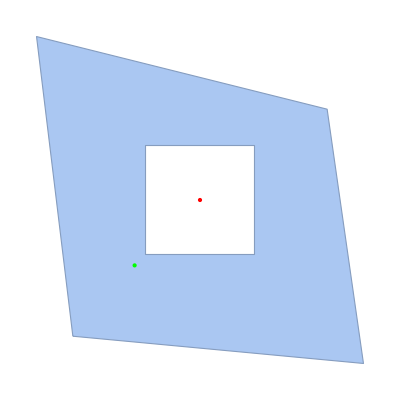

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 2

```mathematica
nHoles=1;
exteriorBoundaryPoints={{-1, -1},{1, -1},{1, 1},{-1, 1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{-1/2, -1/2},{1/2, -1/2},{1/2, 1/2},{-1/2, 1/2}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={{5,6,7,8}};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
```

```mathematica
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
```

```mathematica
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];;
```

```mathematica
pointsInHoles={{0.,0.}};
```

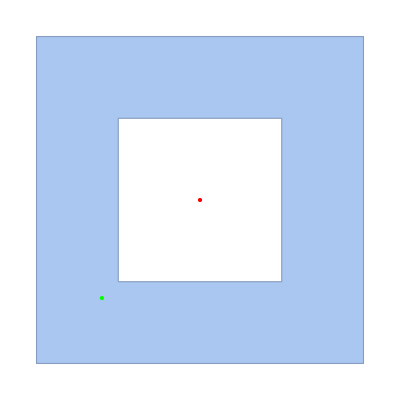

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 3

```mathematica
nHoles=1;
exteriorBoundaryPoints={{-1, -1},{1, -1},{1, 1},{-1, 1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{-1/4, -1/4},{1/4, -1/4},{1/4, 1/4},{-1/4, 1/4}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={{5,6,7,8}};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
```

```mathematica
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
```

```mathematica
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];;
```

```mathematica
pointsInHoles={{0.,0.}};
```

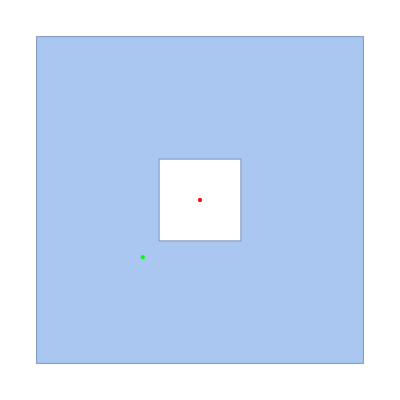

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 4

```mathematica
nHoles=1;
exteriorBoundaryPoints={{-1, -1},{1, -1},{1, 1},{-1, 1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{0,0},{-1/4, 2/3},{-1/2, 2/3},{-2/3, 1/4}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={{5,6,7,8}};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
```

```mathematica
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
```

```mathematica
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];;
```

```mathematica
pointsInHoles={{-.35,.4}};
```

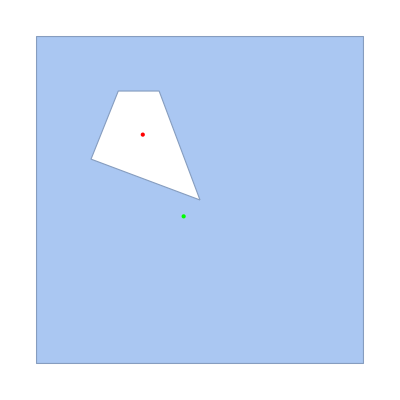

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 5

```mathematica
innerRadius = 1/3;
nMesh = 5;
refinementLevel = 3;
```

```mathematica
pointInHoleSeq=Table[{0.,0.},{nMesh}];
omega0Seq=Table[{0.,(1.+innerRadius)/2},{nMesh}];
```

```mathematica
TSeq = Table[,{nMesh}];
regionSeq= Table[,{nMesh}];
regionSkeletonSeq=Table[,{nMesh}];
regionVerticesSeq = Table[,{nMesh}];
extVSeq = Table[,{nMesh}];
intVSeq = Table[,{nMesh}];
For[iter=1, iter≤ nMesh,iter++,
{regionVerticesSeq[[iter]], extVSeq[[iter]], intVSeq[[iter]]} = PolygonalAnnulus[iter + 2, 1/3];
regionSeq[[iter]]=BoundaryMeshRegion[regionVerticesSeq[[iter]], Line[Append[extVSeq[[iter]],extVSeq[[iter,1]] ]], Line[Append[intVSeq[[iter]],intVSeq[[iter,1]]]] ];
TSeq[[iter]] = Evaluate[AcuteTriangulateAnnulus[regionVerticesSeq[[iter]], extVSeq[[iter]], intVSeq[[iter]] ]];
TSeq[[iter]] = Nest[RefineTriangulation, TSeq[[iter]], refinementLevel];
];
```

```mathematica
For[iter=1, iter≤ nMesh,iter++,regionSkeletonSeq[[iter]] = {MeshCoordinates[regionSeq[[iter]]], MeshCells[regionSeq[[iter]],1]}
];
```

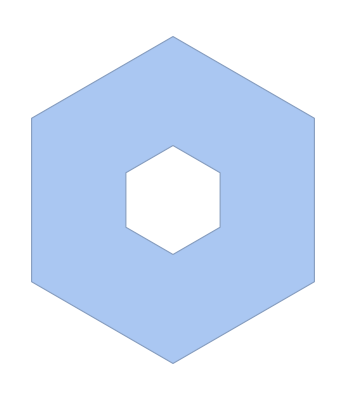

```mathematica
regionSeq[[4]]
```

#### Test Region 6

```mathematica
nHoles=1;
exteriorBoundaryPoints=N/@{{1/3,1/4},{3,0},{8/3,7/3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={StarPoints[{1.5,1.5},.2,.6,5]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

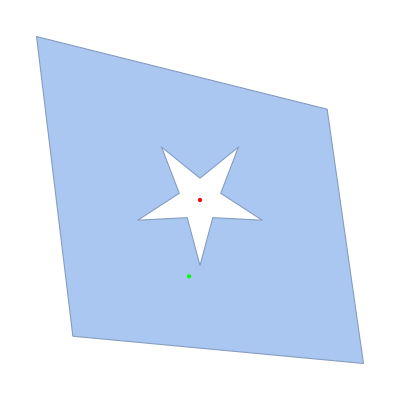

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 7

```mathematica
nHoles=1;
exteriorBoundaryPoints=StarPoints[{0,0},1,2,5];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={StarPoints[{0,0},.2,.6,5]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

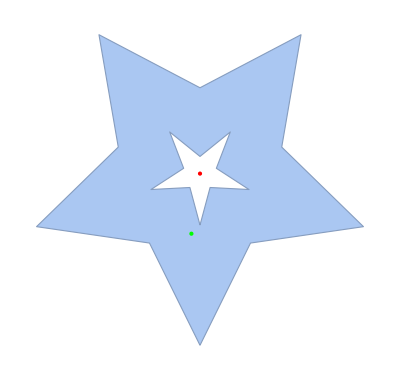

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 8

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{2,0},{3,1},{3,2},{2,3},{0,3},{0,2},{1,1.5},{0,1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{2,1.5},.5,3]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

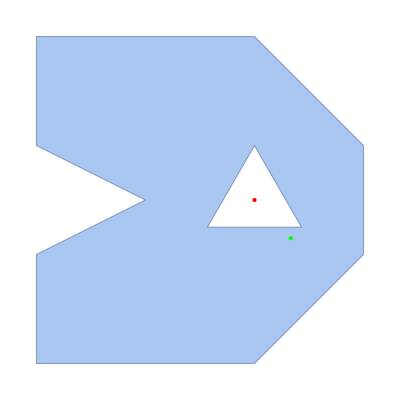

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 9

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{2,0},{3,1},{3,2},{2,3},{0,3},{0,2},{1,1.5},{0,1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={StarPoints[{2,1.5},.3,.6,5]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

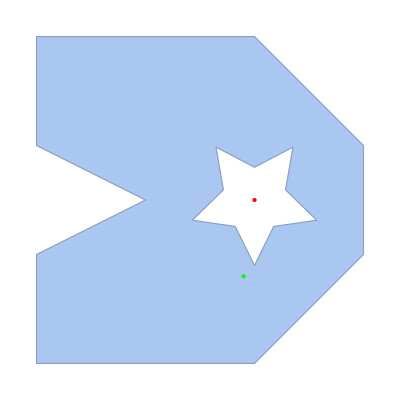

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 10

```mathematica
nHoles=1;
exteriorBoundaryPoints=StarPoints[{0,0},1.8,3,6];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={StarPoints[{0,0},.3,.6,5]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

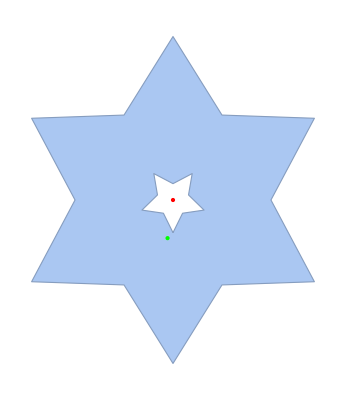

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 11

```mathematica
nHoles=1;
exteriorBoundaryPoints=CirclePoints[{0,0},1,3];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{.3,0},.2,3]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

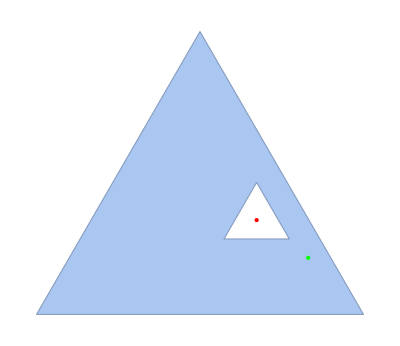

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 12

```mathematica
nHoles=1;
exteriorBoundaryPoints=CirclePoints[{0,0},1,8];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={(RotationMatrix[Pi/6].#&/@CirclePoints[{0,0},.2,3])+.1};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.1,-.1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

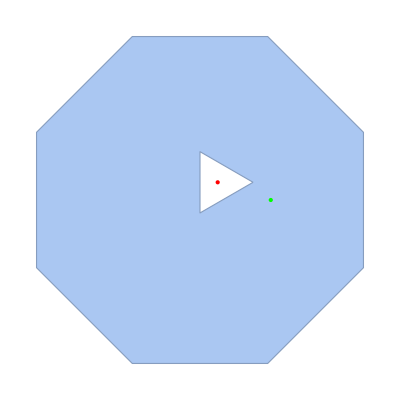

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 13

```mathematica
nHoles=1;
exteriorBoundaryPoints=StarPoints[{2,1.5},6,10,5];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{0,0},{2,0},{3,1},{3,2},{2,3},{0,3},{0,2},{1,1.5},{0,1}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{-1,-1},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

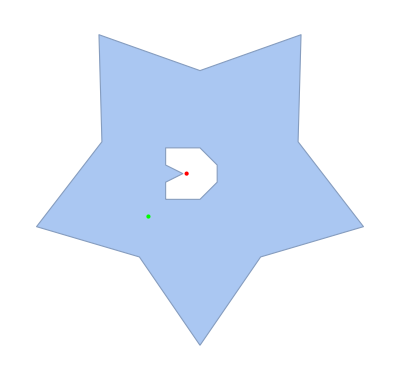

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 14

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{6,0},{9,4},{5,6},{2,2},{-1,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{0,1.5},{5.5,1.5},{5.5,1.7},{0,1.7}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.2,-.2},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

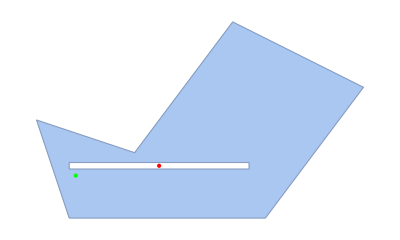

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 15

```mathematica
nHoles=1;
exteriorBoundaryPoints=CirclePoints[{0,0},10,4];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{-2,-4},{0,-1},{2,-4},{2,4},{0,1},{-2,4}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.2,-.2},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

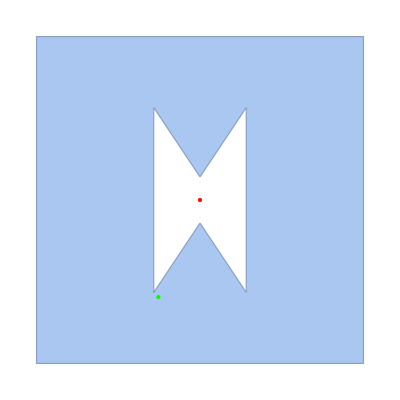

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 16

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{2,0},{3,2},{4,0},{7,5},{4,6},{0,6}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{.5,4},{2.3,3.8},{3,4.7},{1.8,5}}};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.2,-.2},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

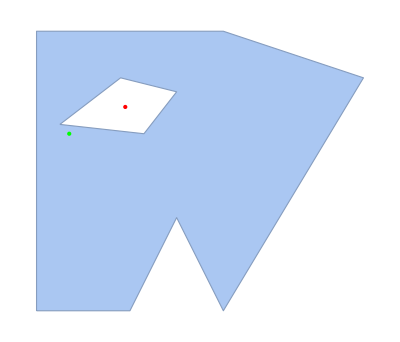

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region BROKEN

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{2,0},{3,3},{4,0},{7,5},{4,6},{0,6}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{.5,4},{2.3,3.8},{3,4.7},{1.8,5},{2.1,4.5}}+Table[{.5,0},{5}]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.2,-.2},{i,nHoles}];
pointsInHoles={{2.44,4.2}};
```

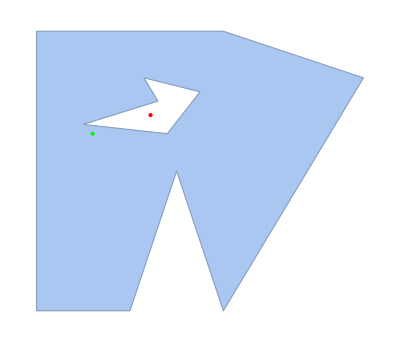

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region BROKEN

```mathematica
nHoles=1;
exteriorBoundaryPoints={{0,0},{4,2},{2,0},{5,0},{6,5},{2,2.5},{.5,3},{-.5,1.2}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={RotationMatrix[Pi/4].#&/@CirclePoints[{0,0},.3,4]+Table[{1,1.7},{4}]};
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{.2,-.2},{i,nHoles}];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

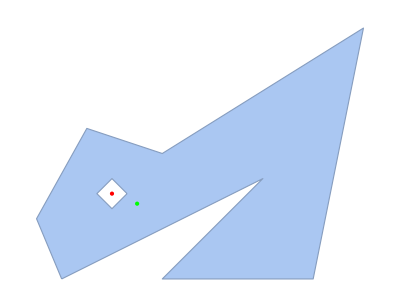

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

### Genus 2 Examples

#### Test Region 1

```mathematica
omega0Seq={{1.1,1.1},{4.,1.2928932188134525},{4.5,.5}};
nHoles=2;
nClasses=nHoles+1;
pointsInHoles={{.75,.75},{4.,2.},{.75,.75}}; (* Last element can be any of the previous elements because the outer partition contains all holes *)
exteriorVertices = {1,2,3,4};
interiorVerticesByHole = {{5,6,7,8},{9,10,11,12}};
regionVertices ={{0.,0.},{5.,0.},{5.,3.},{0.,3.},
{.5,.5},{1.,.5},{1.,1.},{.5,1.},
{4.353553390593274,1.6464466094067263},{4.353553390593274,2.353553390593274},{3.646446609406726,2.353553390593274},{3.646446609406726,1.6464466094067263}};
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
```

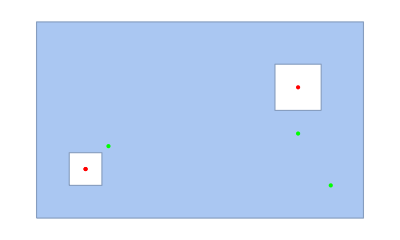

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 2

```mathematica
omega0Seq={{1.1,1.1},{3.5,1.5},{4.5,.5}};
nHoles=2;
nClasses=nHoles+1;
pointsInHoles={{.75,.75},{4.,2.},{.75,.75}}; (* Last element can be any of the previous elements because the outer partition contains all holes *)
exteriorVertices = {1,2,3,4};
interiorVerticesByHole = {{5,6,7,8},{9,10,11,12}};
regionVertices ={{0.,0.},{5.,0.},{5.,3.},{0.,3.},
{.5,.5},{1.,.5},{1.,1.},{.5,1.},
{4.,1.5},{4.5,2},{4.,2.5},{3.5,2}};
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
```

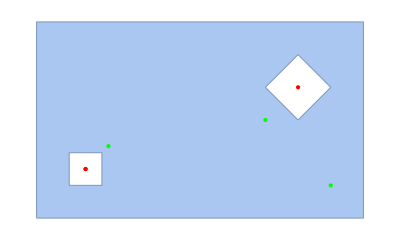

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 3

```mathematica
omega0Seq={{1.1,1.1},{3,1.5},{4.5,.5}};
nHoles=2;
hole2Points=Table[.2*{Cos[t],Sin[t]}+{2.5,1.5},{t,0,2*Pi-.0000001,2*Pi/12}];
nClasses=nHoles+1;
pointsInHoles={{.75,.75},{2.5,1.5},{.75,.75}}; (* Last element can be any of the previous elements because the outer partition contains all holes *)
exteriorVertices = {1,2,3,4};
interiorVerticesByHole = {{5,6,7,8},Range[Length[hole2Points]]+8};
regionVertices =Join[{{0.,0.},{5.,0.},{5.,3.},{0.,3.},
{.5,.5},{1.,.5},{1.,1.},{.5,1.}},hole2Points];
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
```

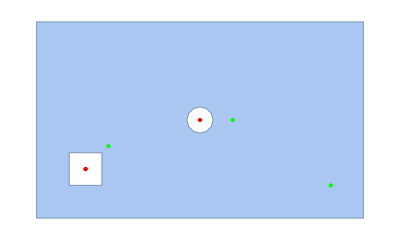

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region Stars

```mathematica
exteriorBoundaryPoints={{0.,0.},{5.,0.},{5.,3.},{0.,3.}};
nCirclePoints = 5;
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={Riffle[Map[RotationMatrix[-(Pi/nCirclePoints)].#&,CirclePoints[.4, nCirclePoints] ], CirclePoints[.15, nCirclePoints]] + Table[{1.67,2},{nCirclePoints*2}],
Riffle[Map[RotationMatrix[-(Pi/nCirclePoints)].#&,CirclePoints[.6, nCirclePoints] ], CirclePoints[.2, nCirclePoints]] + Table[{3.5,1},{nCirclePoints*2} ]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ],
Range[Length[exteriorBoundaryPoints]+Length[holePointsList[[1]] ]+1, Length[holePointsList[[1]] ] +Length[holePointsList[[2]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
convex=False;
```

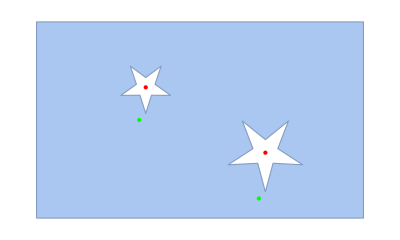

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 4

```mathematica
exteriorBoundaryPoints={{1/3,1/4},{3,0},{8/3,7/3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{.9,2.1},.3,4],StarPoints[{2.1,.9},.4,.15,5.]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ],
Range[Length[exteriorBoundaryPoints]+Length[holePointsList[[1]] ]+1, Length[holePointsList[[1]] ] +Length[holePointsList[[2]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
convex=False;
```

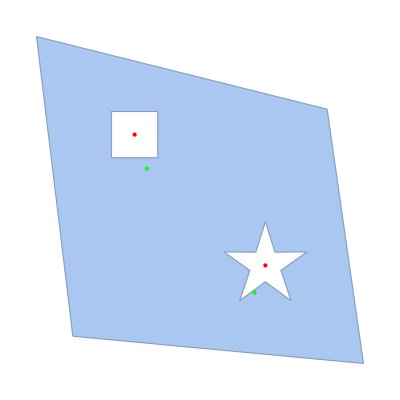

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 5

```mathematica
exteriorBoundaryPoints=CirclePoints[{1,1},2, 6];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{.9,2.1},.3,3],CirclePoints[{2.1,.9},.3,3]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ],
Range[Length[exteriorBoundaryPoints]+Length[holePointsList[[1]] ]+1, Length[holePointsList[[1]] ] +Length[holePointsList[[2]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
convex=True;
```

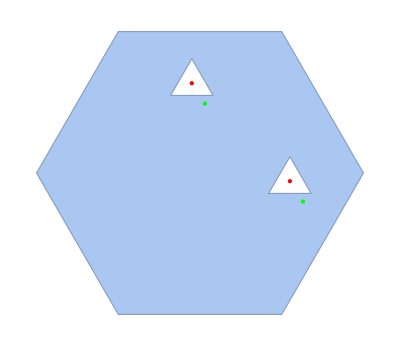

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 6

```mathematica
exteriorBoundaryPoints={{0,0},{2,0},{3,2},{2,3},{0,3},{1,2},{0,1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{1.5,1},.2,9],CirclePoints[{1.6,2.5},.2,3]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ],
Range[Length[exteriorBoundaryPoints]+Length[holePointsList[[1]] ]+1, Length[holePointsList[[1]] ] +Length[holePointsList[[2]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
convex=False;
```

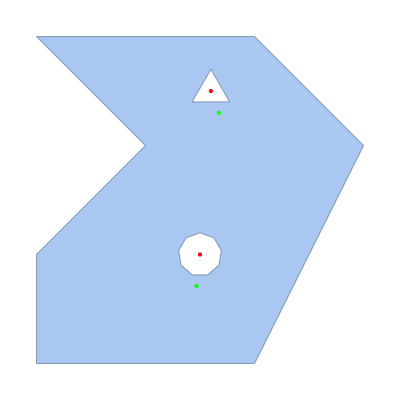

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 7

```mathematica
exteriorBoundaryPoints=StarPoints[{0,0},1.3,3,5];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={CirclePoints[{-.6,-.3},.25,3],CirclePoints[{.5,.5},.25,9]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole={Range[Length[exteriorBoundaryPoints]+1, Length[holePointsList[[1]] ] + Length[exteriorBoundaryPoints] ],
Range[Length[exteriorBoundaryPoints]+Length[holePointsList[[1]] ]+1, Length[holePointsList[[1]] ] +Length[holePointsList[[2]] ] + Length[exteriorBoundaryPoints] ]};
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.1,-.1},{i,nHoles}];
convex=False;
```

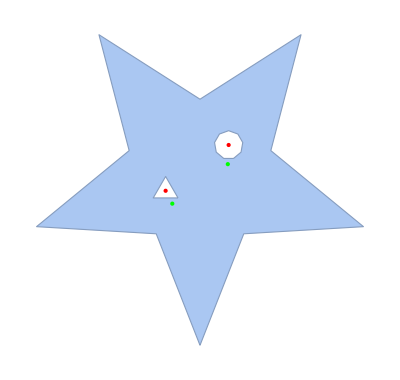

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

### Higher Genus Examples

#### Test Region 1

```mathematica
exteriorBoundaryPoints={{0,0},{1,0},{1.3,1},{2.7,1},{3,0},{4,0},{4,3},{3,3},{2.7,2},{1.3,2},{1,3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={
Map[RotationMatrix[0].#+{.5,1.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[Pi/2].#+{3.5,2.5}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{3.5,.5}&,CirclePoints[.1, 3]]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[,{nHoles}];
sum=nExteriorBoundaryPoints;
For[i=1,i≤nHoles,i++,
interiorVerticesByHole[[i]]=Range[sum+1, sum+Length[holePointsList[[i]] ]] ;
sum=sum+Length[holePointsList[[i]] ];
];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],
Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ],
Line[Append[interiorVerticesByHole[[3]],interiorVerticesByHole[[3, 1]]] ]];
omega0Seq=Table[holePointsList[[i,1]]+{-.15,-.15},{i,nHoles}];
convex=False;
```

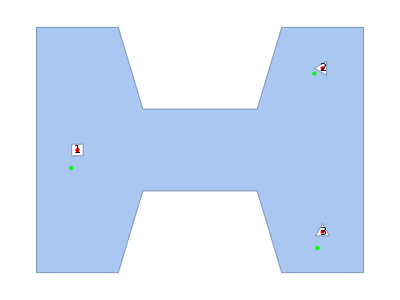

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq,ShowHoleNumbers[pointsInHoles]]
```

#### Test Region 2

```mathematica
exteriorBoundaryPoints={{0,0},{1,0},{1.3,1},{2.7,1},{3,0},{4,0},{4.3,1},{5.7,1},{6,0},{7,0},{7,3},{6,3},{5.7,2},{4.3,2},{4,3},{3,3},{2.7,2},{1.3,2},{1,3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={
Map[RotationMatrix[0].#+{.5,1.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[Pi/2].#+{3.5,2.5}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{3.5,.5}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{6.5,2.5}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{6.5,.5}&,CirclePoints[.1, 3]]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[,{nHoles}];
sum=nExteriorBoundaryPoints;
For[i=1,i≤nHoles,i++,
interiorVerticesByHole[[i]]=Range[sum+1, sum+Length[holePointsList[[i]] ]] ;
sum=sum+Length[holePointsList[[i]] ];
];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0]];
omega0Seq=Table[holePointsList[[i,1]]+{-.15,-.15},{i,nHoles}];
convex=False;
```

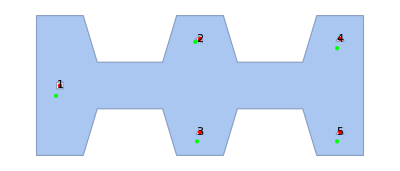

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq,ShowHoleNumbers[pointsInHoles]]
```

#### Test Region 3

```mathematica
nHoles=4;
nOuterCirclePoints=9;
nInnerCirclePoints=4;
nHolePointsList=Table[nInnerCirclePoints,{nHoles}];
exteriorBoundaryPoints=CirclePoints[{1,Pi/2.},nOuterCirclePoints];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList=Table[CirclePoints[CirclePoints[{0.6, Pi/2.},nHoles][[i]],{.1, Pi/2.},nInnerCirclePoints],{i,nHoles}];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[nExteriorBoundaryPoints+Range[nHolePointsList[[i]] ]+Sum[nHolePointsList[[j]],{j,i-1}],{i,nHoles}];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0]];
omega0Seq=Table[holePointsList[[i,1]]+{-.15,-.15},{i,nHoles}];
convex=False;
```

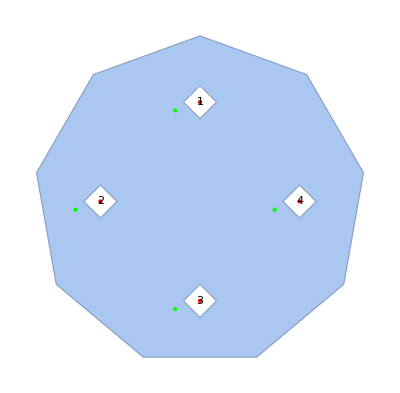

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq,ShowHoleNumbers[pointsInHoles]]
```

#### Test Region 4

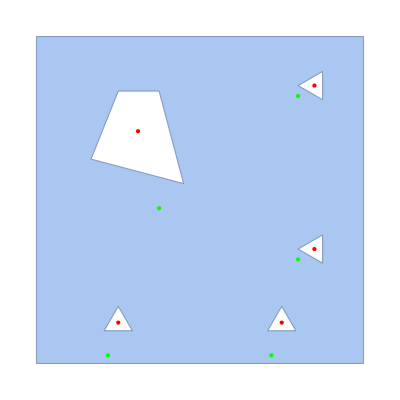

```mathematica
exteriorBoundaryPoints={{-1, -1},{1, -1},{1, 1},{-1, 1}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={{{-.1,.1},{-1/4, 2/3},{-1/2, 2/3},{-2/3, 1/4}},
Map[RotationMatrix[Pi/2].#+{.7,-.3}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{.5,-.75}&,CirclePoints[.1, 3]],
Map[RotationMatrix[0].#+{-.5,-.75}&,CirclePoints[.1, 3]],
Map[RotationMatrix[Pi/2].#+{.7,.7}&,CirclePoints[.1, 3]]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[,{nHoles}];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
sum=nExteriorBoundaryPoints;
For[i=1,i≤nHoles,i++,
interiorVerticesByHole[[i]]=Range[sum+1, sum+Length[holePointsList[[i]] ]] ;
sum=sum+Length[holePointsList[[i]] ];
];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0]];
omega0Seq=Table[holePointsList[[i,1]]+{-.15,-.15},{i,nHoles}];
convex=False;
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 5

```mathematica
nHoles=3;
nHole1Points=12;
nHole2Points=12;
nHole3Points=12;
exteriorBoundaryPoints={{0.,0.},{5.,0.},{5.,3.},{0.,3.}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
hole1Points=Table[.2*{Cos[t],Sin[t]}+{1.5,1},{t,0,2*Pi-.0000001,2*Pi/nHole1Points}];
hole2Points=Table[.2*{Cos[t],Sin[t]}+{2.5,1.5},{t,0,2*Pi-.0000001,2*Pi/nHole2Points}];
hole3Points=Table[.2*{Cos[t],Sin[t]}+{3.5,2},{t,0,2*Pi-.0000001,2*Pi/nHole3Points}];
nClasses=nHoles+1;
```

```mathematica
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole = {Range[nHole1Points]+4,Range[nHole1Points]+4+nHole1Points,Range[nHole3Points]+4+nHole1Points+nHole2Points};
regionVertices =Join[exteriorBoundaryPoints,hole1Points,hole2Points,hole3Points];
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Line[Append[interiorVerticesByHole[[1]],interiorVerticesByHole[[1, 1]]] ],
Line[Append[interiorVerticesByHole[[2]],interiorVerticesByHole[[2, 1]]] ],
Line[Append[interiorVerticesByHole[[3]],interiorVerticesByHole[[3, 1]]] ]];
```

```mathematica
omega0Seq={hole1Points[[1]]+{.1,0},
hole2Points[[1]]+{.1,0},
hole3Points[[1]]+{.1,0},
exteriorBoundaryPoints[[1]]+{.1,.1}};
```

```mathematica
omega0Seq={{1.1,1.1},{3,1.5},{4.5,.5}};
pointsInHoles={Mean[hole1Points],Mean[hole2Points],Mean[hole3Points]}; (* Last element can be any of the previous elements because the outer partition contains all holes *)
```

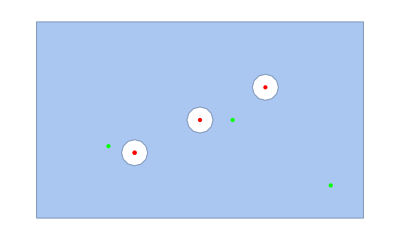

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

#### Test Region 6

```mathematica
exteriorBoundaryPoints={{0,0},{1,0},{1.3,1},{2.7,1},{3,0},{4,0},{4.3,1},{5.7,1},{6,0},{7,0},{7,3},{6,3},{5.7,2},{4.3,2},{4,3},{3,3},{2.7,2},{1.3,2},{1,3},{0,3}};
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList={
Map[RotationMatrix[0].#+{.5,2.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{.5,.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{3.5,2.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{3.5,.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{6.5,2.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{6.5,.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{2,1.5}&,CirclePoints[.1, 4]],
Map[RotationMatrix[0].#+{5,1.5}&,CirclePoints[.1, 4]]};
nHoles=Length[holePointsList];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[,{nHoles}];
sum=nExteriorBoundaryPoints;
For[i=1,i≤nHoles,i++,
interiorVerticesByHole[[i]]=Range[sum+1, sum+Length[holePointsList[[i]] ]] ;
sum=sum+Length[holePointsList[[i]] ];
];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];; 
region=BoundaryMeshRegion[regionVertices,Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0]];
omega0Seq=Table[holePointsList[[i,1]]+{-.15,-.15},{i,nHoles}];
convex=False;
```

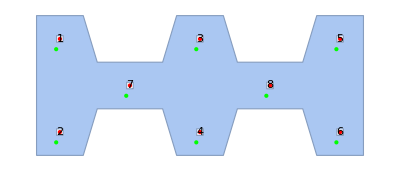

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq,ShowHoleNumbers[pointsInHoles]]
```

#### Test Region 7

```mathematica
nHoles=7;
nOuterCirclePoints=9;
nInnerCirclePoints=4;
nHolePointsList=Table[nInnerCirclePoints,{nHoles}];
exteriorBoundaryPoints=CirclePoints[{1,Pi/2.},nOuterCirclePoints];
nExteriorBoundaryPoints=Length[exteriorBoundaryPoints];
holePointsList=Table[CirclePoints[CirclePoints[{0.6, Pi/2.},nHoles][[i]],{.05, Pi/2.},nInnerCirclePoints],{i,nHoles}];
nClasses=nHoles+1;
exteriorVertices = Range[nExteriorBoundaryPoints];
interiorVerticesByHole=Table[nExteriorBoundaryPoints+Range[nHolePointsList[[i]] ]+Sum[nHolePointsList[[j]],{j,i-1}],{i,nHoles}];
regionVertices=Join[exteriorBoundaryPoints,Delete[holePointsList,0] ];
region=BoundaryMeshRegion[regionVertices,
Line[Append[exteriorVertices,exteriorVertices[[1]]]],Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
omega0Seq=Table[holePointsList[[i,1]]+{0,.03},{i,nHoles}];
(*omega0Seq=Table[holePointsList[[i,1]]+{0,.01},{i,nHoles}];*) (*Gives "omega0notcontainedincontainedface" error when building SlittedLambdaGraph*) 
pointsInHoles=Table[Mean[holePointsList[[i]] ],{i,nHoles}];
```

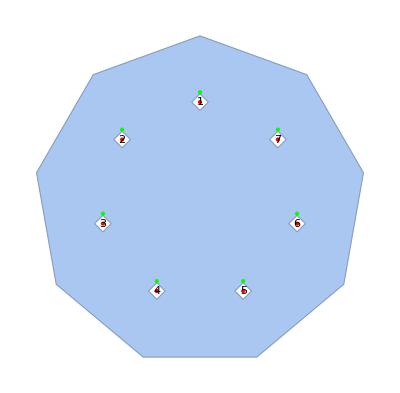

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq,ShowHoleNumbers[pointsInHoles]]
```

#### Test Region 8

```mathematica
(* From SaarEric5820.1.nb *)
```

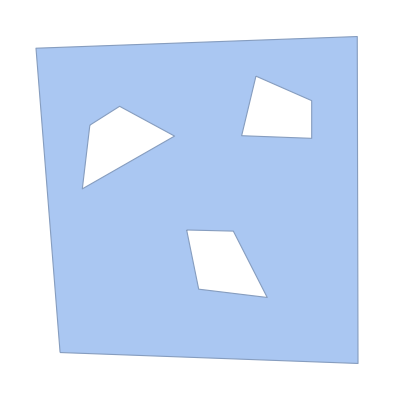
```mathematica
region=-Graphics-;
```

```mathematica
regionVertices={{-3.6799999999999997,-3.6799999999999997},{4.23,-3.9699999999999998},{4.210000000000001,4.700000000000001},{-4.32,4.390000000000001},{-0.3200000000000003,-0.4299999999999997},{0.9199999999999999,-0.45999999999999996},{1.8200000000000003,-2.2199999999999998},{0.,-2.},{-3.09,0.6600000000000001},{-0.6399999999999997,2.0600000000000005},{-2.1,2.8500000000000005},{-2.89,2.3500000000000005},{1.5200000000000005,3.6500000000000004},{1.1400000000000006,2.0700000000000003},{3.,2.},{3.,3.}};
```

```mathematica
exteriorVertices={1,2,3,4};
interiorVerticesByHole={{5,6,7,8},{9,10,11,12},{13,14,15,16}};
```

```mathematica
nHoles=Length[interiorVerticesByHole];
```

```mathematica
(* pointsInHoles={Mean[Sbound1[[1]]],Mean[Sbound2[[1]]],Mean[Sbound3[[1]]]};*)
pointsInHoles={{0.605,-1.2774999999999999},{-2.18,1.9800000000000004},{2.165,2.68}};
(* omega0Seq={Sbound1[[1,3]]-{0,0.2},Sbound2[[1,1]]-{0,0.2},Sbound3[[1,3]]-{0,0.2}};*)
omega0Seq={{1.8200000000000003,-2.42},{-3.09,0.46000000000000013},{3.,1.8}};
```

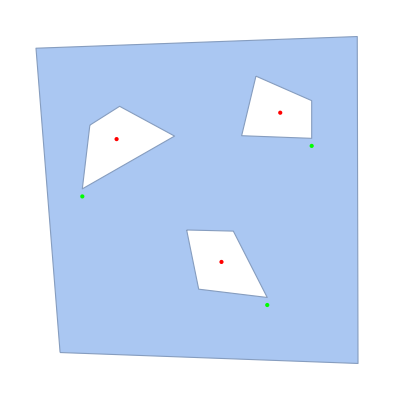

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

## Test Main for Genus 1 Examples

```mathematica
refinementLevel=2;
```

```mathematica
{regionSkeleton,T,f,Lambda,LambdaGraph,GSBValuesExtended,phiValuesExtended,interiorNonslitTriangles,interpolatedGSBValueMeshExtended,h2,newPoints,cleaned,radius,slitVertices}=Main[region,regionVertices,interiorVerticesByHole,exteriorVertices,nHoles,pointsInHoles,omega0Seq,refinementLevel, False];
```

```mathematica
h = Table[i,{i,0,1,.05}];
```

```mathematica
GraphicsGrid[{{
Show[
LinearSplineLevelCurves2D[T[[3]], f[Delete[T[[1, #]],0]]& , h, T[[1]], "AvocadoColors", Transparent],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]
],
Show[LinearSplineLevelCurves2D[interiorNonslitTriangles, interpolatedGSBValueMeshExtended[[#]]&, h2, T[[1]], "CandyColors",  RGBColor[0.84,0.84,0.84]],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]],
Show[LinearSplineLevelCurves2D[interiorNonslitTriangles, interpolatedGSBValueMeshExtended[[#]]&, h2, T[[1]], "CandyColors", Transparent],
LinearSplineLevelCurves2D[T[[3]], f[Delete[T[[1, #]],0]]& , h, T[[1]], "AvocadoColors", Transparent],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]]
}}]
```

```mathematica
Show2Skeleton[T]
```

```mathematica
Show[Plot[,{x,-radius, radius}, PlotRange->radius, AspectRatio->1],ListPlot[newPoints],Show[Graphics[{Red, PointSize[.008], #}]& /@ Point/@newPoints[[slitVertices]] ] ]
```

## Import Triangulation Data from Julia

```mathematica
fullFileStem="/Users/eric/Code/planar-domains/regions/our_example/our_example";
```

```mathematica
{regionVertices,regionBdryMarkers,regionEdges,pointsInHoles,coordinates,bdryMarkers,triangles,triangulationTopology}=readData[fullFileStem];
```

```mathematica
{exteriorVertices,interiorVerticesByHole,region,regionSkeleton,nHoles,nClasses,omega0Seq}=makeRegionData[regionVertices,regionEdges,pointsInHoles,50];
```

## Line-by-Line Function Version for Genus n Examples

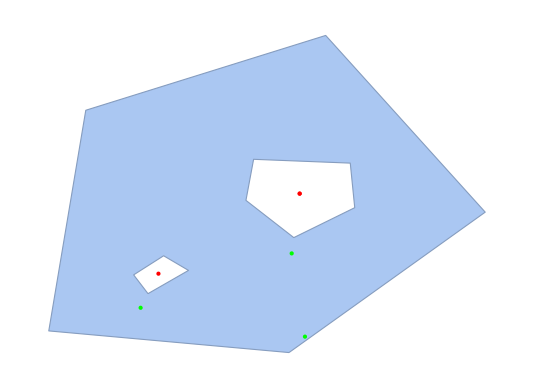

```mathematica
Show[region,Graphics[{Red,#}]&/@Point/@pointsInHoles,Graphics[{Green,#}]&/@Point/@omega0Seq]
```

```mathematica
(* Triangulate using imported data from Julia program TriVor.jl *)
showImages=True;
h = Table[i,{i,0,1,.01}];
T={coordinates,Partition[Flatten[EdgesWrapCompiled/@triangles],2],triangles};
T[[2]] = Union[Sort/@T[[2]] ]; (* Remove duplicated edges *)
```

```mathematica
(*(* Triangulate OLD METHOD *)
showImages=True;
refinementLevel=3;
h = Table[i,{i,0,1,.025}];
TUnrefined=AcuteTriangulate[region,pointsInHoles];
T=Nest[RefineTriangulation,TUnrefined,refinementLevel];
T[[2]] = Union[Sort/@T[[2]] ]; (* Remove duplicated edges *)regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};*)
```

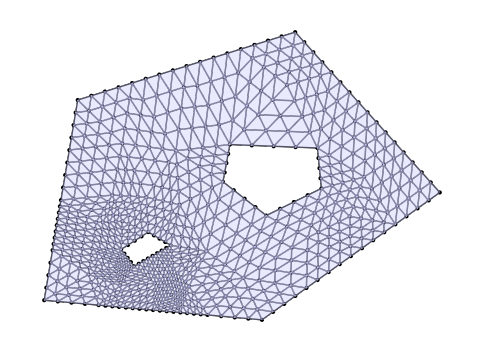

```mathematica
If[showImages,Show2Skeleton[T]]
```

```mathematica
(*If[showImages,Show[VoronoiMesh[T[[1]]],Show2Skeleton[T]]]*)
```

```mathematica
(* Compute f *)
(*triangulationTopology=BuildTriangulationTopologyNDLUACompiled[T[[3]] ];*)
(*triangulationTopology=topologyImported;*)
{interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation}=InteriorAndBoundaryEdges[T[[3]],triangulationTopology];
eMesh=ToElementMesh["Coordinates"->T[[1]],"MeshElements"->{TriangleElement[T[[3]] ]}];
```

```mathematica
exteriorBoundary = Line[regionVertices[[#]]&/@ Append[exteriorVertices,exteriorVertices[[1]] ] ];
interiorBoundaries=Table[Line[regionVertices[[#]]&/@ Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i,1]] ] ],{i,nHoles}];
Γ1=DirichletCondition[u[x,y] == 1, RegionDistance[exteriorBoundary, {x,y}] < 1*10^(-5)];Γ2=DirichletCondition[u[x,y]==0,Min[RegionDistance[#, {x,y}]&/@interiorBoundaries] < 1*10^(-5)];
```

```mathematica
f=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==0,Γ1,Γ2 },u,{x,y}∈eMesh];
fValues=f@@@T[[1]];
```

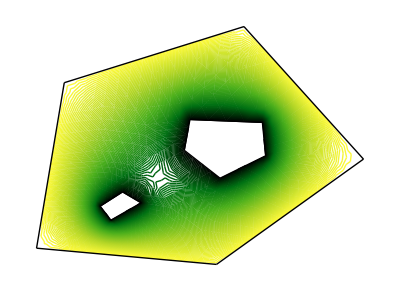

```mathematica
If[showImages,Show[
LinearSplineLevelCurves2D[T[[3]], f[Delete[T[[1, #]],0]]& , h, T[[1]], "AvocadoColors", Transparent],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]
]]
```

```mathematica
(*Construct Lambda*)
Lambda=BuildLambda[T,exteriorVertices,interiorVerticesByHole,regionVertices];
```

```mathematica
(* Compute contained vertices and contained faces *)
rmf=RegionMember[region];
containedVerticesIndicator=rmf/@Lambda[[1]];
containedVertices=Pick[Range[Length[Lambda[[1]]]],containedVerticesIndicator];
If[showImages,Show[Show2Skeleton[Lambda,{},{containedVertices,{},{}}],Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]]]
containedFaces=ContainedFaces[Lambda[[3]],containedVertices];
paddedPolygons=PadPolygonsToMatrix[Lambda[[3]] ];
toRightOfEdgeTriAssociation=BuildEdgeToRightTriangulationAssociation[T[[3]] ];
toRightOfEdgePolyAssociation=BuildEdgeToRightPolygonsAssociation[paddedPolygons];
conductanceAssociation=BuildConductanceAssociation[T[[3]],interiorEdgesOrientedTriangulation,toRightOfEdgeTriAssociation,T[[1]]];
```

```mathematica
omega0Seq
```

{{1058.69,390.567},{1517.34,566.044},{1508.,215.}}

```mathematica
(* Build the Lambda graph *)
{LambdaGraph,omega0n,slitVertices}=
BuildSlittedWeightedVoronoiGraph[Lambda,containedVertices,containedFaces,omega0Seq[[1]],pointsInHoles[[1]],toRightOfEdgePolyAssociation];
```

BuildSlittedWeightedVoronoiGraph::omega0notincontainedface: omega0 is not contained in any containedFace

Set::shape: Lists {LambdaGraph,omega0n,slitVertices} and $Failed are not the same shape.

```mathematica
(* Find singular level curves and partition region *)
boundaryVertices=Union[Flatten[boundaryEdgesOrientedTriangulation] ];
interiorVertices=Complement[Range[Length[T[[1]] ] ],boundaryVertices];
vertexTopology=VertexTopologyBuilderCompiled[Length[T[[1]] ],T[[2]] ];
```

```mathematica
interiorVertices[[1]]
```

1

```mathematica
IndexFunction[1, vertexTopology, T[[1]]]
```

2

```mathematica
indexFunctionValues=IndexFunction[#,vertexTopology,T[[1]] ]&/@interiorVertices;
```

```mathematica
indexFunctionValues
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
singularVerticesInd=Flatten[Position[indexFunctionValues,x_/;x≠2]];
nSingularVertices=Length[singularVerticesInd];
singularVertices=interiorVertices[[singularVerticesInd]];
```

```mathematica
singularHeights=Sort[f@@@T[[1,singularVertices]]];
nSingularHeights=Length[singularHeights];
```

```mathematica
singularHeights
```

{0.0409438}

```mathematica
TriLevelSets[#, f[Delete[T[[1, #]],0]]&, singularHeights[[1]],T[[1]]]&/@ T[[3]]
```

```mathematica
colorList=ColorData["NeonColors"]/@(Range[nSingularHeights]/nSingularHeights);
If[showImages,Show[
LinearSplineLevelCurves2D[T[[3]],f[Delete[T[[1, #]],0]]&,h,T[[1]], "AvocadoColors", Transparent],
Table[LinearSplineLevelCurve2D[T[[3]],f[Delete[T[[1, #]],0]]&,{singularHeights[[i]]},T[[1]],colorList[[i]],Transparent],{i,nSingularHeights}],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]
]]
```

```mathematica
intersectingTrianglesIndices=Flatten[Position[T[[3]],#]&/@intersectingTriangles];
intersectingTriangles=Cases[T[[3]],t_/;IntersectingQ[t,singularVertices]];
nonsingularTriangleVertices=Table[Complement[intersectingTriangles[[i]],singularVertices],{i,Length[intersectingTriangles]}];
nonsingularfValues=Map[fValues[[#]]&,nonsingularTriangleVertices,{2}];
test=Map[(#[[1]]-singularHeights[[1]])(#[[2]]-singularHeights[[1]])<0&,nonsingularfValues]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[intersectingTriangles].

{True,True,True,True,False,False}

### WIP

```mathematica
conflux=Pick[intersectingTrianglesIndices,test];
```

```mathematica
gammaS={};
gammaSTriangles={};
triangleIndex=conflux[[1]];
AppendTo[gammaS,T[[1,singularVertices[[1]] ]] ];
AppendTo[gammaSTriangles,triangleIndex];
```

```mathematica
triangleIndex
```

1190

```mathematica
gammaS
```

{{2.2114,1.41017}}

```mathematica
gammaSTriangles
```

{1190}

```mathematica
triangleVertexIndices=T[[3,triangleIndex]]
trifValues=f@@@T[[1,T[[3,triangleIndex]]]];
Cycle[v_]:=Mod[v,3]+1
For[v=1,v++,v≤3,
If[(trifValues[[v]]-singularHeights[[1]])(trifValues[[Cycle[v] ]]-singularHeights[[1]])<0,
AppendTo[gammaS,
LineHeightIntersect[T[[1,triangleVertexIndices[[v]] ]],T[[1,triangleVertexIndices[[Cycle[v] ]] ]],trifValues[[v]],trifValues[[Cycle[v] ]],singularHeights[[1]]];
];
triangleIndex=triangulationTopology[[triangleIndex,v]];
Print[ToString@triangleIndex];
Break[];
,];
];
```

{313,1114,1113}

```mathematica
triangleIndex
```

1190

```mathematica
gammaS
```

{{2.2114,1.41017}}

```mathematica
If[(trifValues[[1]]-singularHeights[[1]])(trifValues[[2]]-singularHeights[[1]])<0,
AppendTo[gammaS,
LineHeightIntersect[T[[1,triangleVertexIndices[[1]] ]],T[[1,triangleVertexIndices[[2]] ]],trifValues[[1]],trifValues[[2]],singularHeights[[1]]];
];
triangleIndex=triangulationTopology[[triangleIndex,1]];
,
If[(trifValues[[2]]-singularHeights[[1]])(trifValues[[3]]-singularHeights[[1]])<0,

triangleIndex=triangulationTopology[[triangleIndex,2]];
,
If[(trifValues[[3]]-singularHeights[[1]])(trifValues[[1]]-singularHeights[[1]])<0,

triangleIndex=triangulationTopology[[triangleIndex,3]];
,];
];
];
```

```mathematica
While[True,
trifValues=f@@@T[[1,T[[3,triangle]]]];
If[(trifValues[[1]]-singularHeights[[1]])(trifValues[[2]]-singularHeights[[1]])<0,
triangle=triangulationTopology[[triangle,1]];
,
If[(trifValues[[2]]-singularHeights[[1]])(trifValues[[3]]-singularHeights[[1]])<0,
triangle=triangulationTopology[[triangle,2]];
,
If[(trifValues[[3]]-singularHeights[[1]])(trifValues[[1]]-singularHeights[[1]])<0,
triangle=triangulationTopology[[triangle,3]];
,];
];
];

If[MemberQ[conflux,triangle],Break[];]; (* Break While loop *)
]
```

```mathematica
Show2Skeleton[T,{},{{},{},{conflux[[1]],1192}}]
```

```mathematica
If[showImages,Show[
Show2Skeleton[T,{},{{},{},conflux}],
LinearSplineLevelCurves2D[T[[3]],f[Delete[T[[1, #]],0]]&,h,T[[1]], "AvocadoColors", Transparent],
Table[LinearSplineLevelCurve2D[T[[3]],f[Delete[T[[1, #]],0]]&,{singularHeights[[i]]},T[[1]],colorList[[i]],Transparent],{i,nSingularHeights}],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}]
]]
```

### Iterate over Singular Level Curves

```mathematica
(* Iterate over the singular level curves *)
fluxList=Table[{},{i,nSingularHeights}];
contributingEdgesListList=Table[{},{i,nSingularHeights}];
holeRepresentatives=interiorVerticesByHole[[;;,1]];
holeContainmentByConnectedComponentList=Table[,{i,nSingularHeights}];
connectedComponentsByHeightClass=Table[{},{i,nSingularHeights}];
For[s=1,s≤nSingularHeights,s++,
lowerHeightClass=Flatten[Position[T[[1]],x_/;f@@x<singularHeights[[s]],1] ];
upperHeightClass=Complement[Range[Length[T[[1]] ] ],lowerHeightClass];
lowerHeightClassEdges=UndirectedEdge@@@Cases[T[[2]],x_/;MemberQ[lowerHeightClass,x[[1]] ]&&MemberQ[lowerHeightClass,x[[2]] ] ];
undirectedGraph=Graph[lowerHeightClassEdges];
connectedComponents=Sort/@ConnectedComponents[undirectedGraph];
connectedComponentsByHeightClass[[s]]=connectedComponents;
nConnectedComponents=Length[connectedComponents];
holeContainmentByConnectedComponentList[[s]]=Table[Flatten[Position[holeRepresentatives,#]&/@Intersection[holeRepresentatives,connectedComponents[[i]] ]],{i,nConnectedComponents}];
connectedComponentMeans=Table[Mean[T[[1,connectedComponents[[i]] ]] ],{i,nConnectedComponents}];
crossingEdgesList=Table[Cases[T[[2]],x_/;(MemberQ[connectedComponents[[i]],x[[1]] ]&&MemberQ[upperHeightClass,x[[2]] ])||(MemberQ[connectedComponents[[i]],x[[2]] ]&&MemberQ[upperHeightClass,x[[1]] ])],{i,nConnectedComponents}];
innerVerticesList=Table[Intersection[DeleteDuplicates[Flatten[crossingEdgesList[[i]] ]],connectedComponents[[i]] ],{i,nConnectedComponents}];
contributingEdgesList=Table[FluxContributingEdgesCompiled[innerVerticesList[[i]],fValues,singularHeights[[s]],vertexTopology],{i,nConnectedComponents}];
contributingEdgesListList[[s]]=contributingEdgesList;
fluxList[[s]]=Map[Chop[FluxOnTriangulation[#,conductanceAssociation,f,T[[1]] ] ]&,contributingEdgesList];
]
```

```mathematica
(* Compute fluxes on the interior and exterior boundaries *)
allExteriorVertices=BoundaryConnectedClasses[T,{1}];
intVerticesList=Table[BoundaryConnectedClasses[T,{interiorVerticesByHole[[i,1]]}],{i,Length[interiorVerticesByHole]}];
contributingEdgesIntList=Table[FluxContributingEdgesCompiled[intVerticesList[[i,1]],1- fValues,1.,vertexTopology],{i,Length[interiorVerticesByHole]}];
contributingEdgesExt=FluxContributingEdgesCompiled[allExteriorVertices[[1]],fValues,1.,vertexTopology];
fluxInt=Table[FluxOnTriangulation[contributingEdgesIntList[[i]],conductanceAssociation,f,T[[1]] ],{i,Length[interiorVerticesByHole]}];
fluxExt={FluxOnTriangulation[contributingEdgesExt,conductanceAssociation,f,T[[1]] ]};
PrependTo[fluxList,fluxInt];
AppendTo[fluxList,fluxExt];
```

```mathematica
PrependTo[holeContainmentByConnectedComponentList,Table[{i},{i,nHoles}]];
AppendTo[holeContainmentByConnectedComponentList,{Table[i,{i,nHoles}]}];
```

```mathematica
(* Check final computation of fluxes *)
fluxList//Column
```

{3.51673,4.74583,4.60748}
{4.50435,3.16691,3.9671}
{7.6712,4.05522}
{12.87}

```mathematica
holeContainmentByConnectedComponentList//Column
```

{{1},{2},{3}}
{{2},{1},{3}}
{{1,2},{3}}
{{1,2,3}}

```mathematica
Print[StringJoin@@Flatten[Table[Join[Table["Flux on element "<>ToString[holeContainmentByConnectedComponentList[[i+1,j]] ] <>" at height level "<>ToString[i]<>":          "<>ToString[fluxList[[i+1,j]] ]<>"\n",{j,Length[holeContainmentByConnectedComponentList[[i+1]]]}],{"\n"}],{i,0,nSingularHeights+1}]]]
```

Flux on element {1} at height level 0:          3.51673
Flux on element {2} at height level 0:          4.74583
Flux on element {3} at height level 0:          4.60748

Flux on element {2} at height level 1:          4.50435
Flux on element {1} at height level 1:          3.16691
Flux on element {3} at height level 1:          3.9671

Flux on element {1, 2} at height level 2:          7.6712
Flux on element {3} at height level 2:          4.05522

Flux on element {1, 2, 3} at height level 3:          12.87

```mathematica
colorList=ColorData["RustTones"]/@((Range[nSingularHeights]-1)/nSingularHeights);
Show[
LinearSplineLevelCurves2D[T[[3]],f[Delete[T[[1, #]],0]]&,h,T[[1]], "AvocadoColors", Transparent],
Table[LinearSplineLevelCurve2D[T[[3]],f[Delete[T[[1, #]],0]]&,{singularHeights[[i]]},T[[1]],colorList[[i]],Transparent],{i,nSingularHeights}],
Graphics/@Map[regionSkeleton[[1, #]]&,regionSkeleton[[2]], {2}],
ShowHoleNumbers[pointsInHoles]
]
```

```mathematica
Show[Show2Skeleton[T],ShowHoleNumbers[pointsInHoles]]
```

```mathematica
Show[region,ShowHoleNumbers[pointsInHoles]]
```

### Run GSB on each Annulus

```mathematica
GraphicsGrid[{{Show2Skeleton[Lambda,{},{containedVertices,,}],Show2Skeleton[Lambda,{},{,,containedFaces}]}}]
```

```mathematica
{LambdaGraphSub,omega0nSub,slitVerticesSub}=
BuildSlittedWeightedVoronoiGraph[Lambda,containedVertices,containedFaces,omega0Seq[[1]],pointsInHoles[[1]],toRightOfEdgePolyAssociation];
```

```mathematica
Show2Skeleton[T,{},{connectedComponentsByHeightClass[[1,1]],,}]
```

```mathematica
(* For use on the partitioned pieces of a higher-genus region *)
```

```mathematica
Main2[region_,regionVertices_,interiorVerticesByHole_,exteriorVertices_,nHoles_,pointsInHoles_,omega0Seq_,refinementLevel_,convex_]:=Module[{TUnrefined,T,regionSkeleton,triangulationTopology,interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation,eMesh,exteriorBoundary,interiorBoundaries,Γ1,Γ2,f,u,fValues,Lambda,containedVertices,containedFaces,LambdaGraph,omega0n,slitVertices,paddedPolygons,toRightOfEdgeTriAssociation,toRightOfEdgePolyAssociation,conductanceAssociationtoRightOfEdgeTriAssociation,conductanceAssociation,LambdaShortestPathFunction,GSBValuesExtended,GSBValues,periodApprox,GSBValuesExtendedNormalized,phiValuesExtended,phiValues,GSBValuePolygons,interpolatedGSBValueMesh,interpolatedGSBValueMeshExtended,TBoundaryVertices,interiorTriangles,GSBMin,GSBMax,h2,slitPolygons,slitPolygonsByIndex,slitTriangles,nonslitTriangles,interiorNonslitTriangles,newPoints,cleaned,radius,holeRegion,rmf,containedVerticesIndicator},
(* Triangulate *)
TUnrefined=AcuteTriangulate[region,pointsInHoles];
T=Nest[RefineTriangulation,TUnrefined,refinementLevel];
T[[2]] = Union[Sort/@T[[2]] ]; (* Remove duplicated edges *)
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};
(* Compute f *)
triangulationTopology=BuildTriangulationTopologyNDLUACompiled[T[[3]] ];{interiorEdgesOrientedTriangulation,boundaryEdgesOrientedTriangulation}=InteriorAndBoundaryEdges[T[[3]],triangulationTopology];
eMesh=ToElementMesh["Coordinates"->T[[1]],"MeshElements"->{TriangleElement[T[[3]] ]}];
exteriorBoundary = Line[regionVertices[[#]]&/@ Append[exteriorVertices,exteriorVertices[[1]] ] ];
interiorBoundaries=Table[Line[regionVertices[[#]]&/@ Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i,1]] ] ],{i,nHoles}];Γ1=DirichletCondition[u[x,y] == 1, RegionDistance[exteriorBoundary, {x,y}] < 1*10^(-5)];Γ2=DirichletCondition[u[x,y]==0,Min[RegionDistance[#, {x,y}]&/@interiorBoundaries] < 1*10^(-5)];f=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==0,Γ1,Γ2 },u,{x,y}∈eMesh];fValues=f@@@T[[1]];
(* Constructing Lambda *)
Lambda=BuildLambda[T,exteriorVertices,interiorVerticesByHole,regionVertices];
(* containedVertices = ContainedVertices[Lambda[[1]],exteriorVertices,interiorVerticesByHole,regionVertices];
If[!convex,
holeRegion=BoundaryMeshRegion[regionVertices,Delete[Table[Line[Append[interiorVerticesByHole[[i]],interiorVerticesByHole[[i, 1]]] ],{i,nHoles}],0] ];
containedVertices=Pick[containedVertices,Not/@RegionMember[holeRegion,Lambda[[1,containedVertices]]]];
];*)
rmf=RegionMember[region];
containedVerticesIndicator=rmf/@Lambda[[1]];
containedVertices=Pick[Range[Length[Lambda[[1]]]],containedVerticesIndicator];
containedFaces=ContainedFaces[Lambda[[3]],containedVertices];
paddedPolygons=PadPolygonsToMatrix[Lambda[[3]] ];
toRightOfEdgeTriAssociation=BuildEdgeToRightTriangulationAssociation[T[[3]] ];
toRightOfEdgePolyAssociation=BuildEdgeToRightPolygonsAssociation[paddedPolygons];
conductanceAssociation=BuildConductanceAssociation[T[[3]],interiorEdgesOrientedTriangulation,toRightOfEdgeTriAssociation,T[[1]]];
{LambdaGraph,omega0n,slitVertices}=
BuildSlittedWeightedVoronoiGraph[Lambda,containedVertices,containedFaces,omega0Seq[[1]],pointsInHoles[[1]],toRightOfEdgePolyAssociation];
(* Compute GSB *)
LambdaShortestPathFunction=FindShortestPath[LambdaGraph,omega0n,All];
GSBValuesExtended=Table[If[MemberQ[containedVertices, i],
GSB2[i,conductanceAssociation,toRightOfEdgePolyAssociation,f,T[[1]],LambdaShortestPathFunction],
 Null], {i, Length[Lambda[[1]] ]}];
GSBValues=DeleteCases[GSBValuesExtended,Null];
periodApprox= Max[Abs[GSBValues]];
GSBValuesExtendedNormalized=GSBValuesExtended;
phiValuesExtended=Exp[2*Pi/periodApprox*(If[MemberQ[containedVertices, #],f[Delete[Lambda[[1,#]], 0]],Null] + I*GSBValuesExtendedNormalized[[#]])]&/@Range[Length[Lambda[[1]] ]];
phiValuesExtended=Map[If[NumberQ[#],#,Null]&,phiValuesExtended,{1}];
phiValues=phiValuesExtended[[containedVertices]];
(* Compute the average (use Wachspress average later for better accuracy) of GSB values on each polygon for interpolation values for points in T *)
GSBValuePolygons=Map[GSBValuesExtended[[#]]&,Lambda[[3,containedFaces]],{2}]; 
interpolatedGSBValueMesh=Mean/@GSBValuePolygons;(* GSBValues on containedFaces polygons *)
interpolatedGSBValueMeshExtended=Table[If[MemberQ[containedFaces,i],Mean[GSBValuesExtended[[#]]&/@Lambda[[3,i]] ],Null], {i,Length[T[[1]] ]}];
TBoundaryVertices=Union[Flatten[boundaryEdgesOrientedTriangulation]];
regionSkeleton={MeshCoordinates[region], MeshCells[region,1]};interiorTriangles=Cases[T[[3]],x_/;!ContainsAny[x,TBoundaryVertices ]];
{GSBMin,GSBMax}={Min[interpolatedGSBValueMesh], Max[interpolatedGSBValueMesh]};
h2=Table[i,{i,GSBMin,GSBMax,.05}];
slitPolygons=Cases[Lambda[[3]], x_/;ContainsAny[x, slitVertices] ];
slitPolygonsByIndex=Flatten[Position[Lambda[[3]], #]&/@ slitPolygons];
slitTriangles=Cases[T[[3]], x_/;ContainsAny[x,slitPolygonsByIndex]];
nonslitTriangles=Complement[T[[3]],slitTriangles];
interiorNonslitTriangles=Cases[nonslitTriangles,x_/;!ContainsAny[x, TBoundaryVertices]];
newPoints=If[SameQ[#,Null],Null,{Re[#],Im[#]}]&/@phiValuesExtended;
cleaned=DeleteCases[newPoints,Null];
radius=Max[Norm/@cleaned];
Return[{regionSkeleton,T,f,Lambda,LambdaGraph,GSBValuesExtended,phiValuesExtended,interiorNonslitTriangles,interpolatedGSBValueMeshExtended,h2,newPoints,cleaned,radius,slitVertices}]
]
```

### Line-by-line testing of TriLevelSets

```mathematica
t=T[[3]][[1]]
```

```mathematica
t={1,2,13}
```

{1,2,13}

```mathematica
perm = Sort[t,f[#1]<f[#2]&]
```

{1,2,13}

```mathematica
values=f[Delete[T[[1, #]],0]]& /@perm
```

{0.,0.100109,0.0647034}

```mathematica
lowVertex = perm[[1]];
midVertex = perm[[2]];
highVertex = perm[[3]];
```

```mathematica
BuildLine[height_] := Block[{},
If[And[values[[1]]< height,  height < values[[2]] ],
Return[
{
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[midVertex]], f[lowVertex], f[midVertex],height ],
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[highVertex]], f[lowVertex], f[highVertex],height ]
}
]
,
If[And[values[[2]]≤ height,  height < values[[3]] ],
Return[
{
LineHeightIntersect[coordinates[[lowVertex]], coordinates[[highVertex]], f[lowVertex], f[highVertex],height ],
LineHeightIntersect[coordinates[[midVertex]], coordinates[[highVertex]], f[midVertex], f[highVertex],height ]
}
]
,
Return[{}]
];
];
];
```

```mathematica
BuildLine/@ singularHeights
```

{{Null,Null}}

```mathematica
h
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}